## 31 March 2011 Thursday

### Overview of exploration of hough-peak-model-based synthetic data

Simulate 30 samples from something like the peak model of the hough transform method with 20 peaks in the samples.  All peaks are present in all samples.  A key factor to a nice ordering appearing is that the sample parameters vary greatly in magnitude.  Further, the range of the multiplied sample parameters must be significantly smaller than the range of mean peak positions in order for the sorted sample plot to look right.

Below is a table reproduced when there are 3 parameters, all with a standard deviation of 0.7 (after sorting by the position of the green peak)

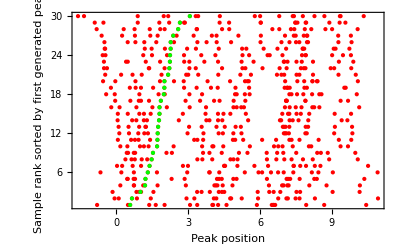

Below that is a table when the parameters had standard deviations of and 1,0.1,0.01  It looks much more like what we observe in the real-life urine spectra.

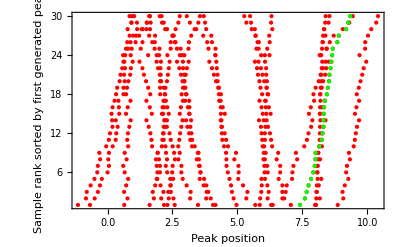

### Set up the global variables that contain the synthetic data for the experiments

s is the sample parameters for each sample

```mathematica
s=Table[{1,.3,.1} RandomReal[NormalDistribution[0,1],3],{30}];
```

a is the peak multipliers for each sample

```mathematica
a=Table[RandomReal[{-1,1},3],{20}];
```

k is the peak mean for each sample

```mathematica
k=RandomReal[{11,0},20];
```

pos is peak positions in each sample

```mathematica
pos=Map[Function[sj,MapThread[Function[{ai,ki},ki+Dot[ai, sj]],{a,k}]],s];
```

### Raw data plot

First, plot the raw data by sample number

```mathematica
allAgainstRawSampleNumber=Flatten[MapThread[Function[{sample,sampleNumber},Map[{sampleNumber,#}&,sample]],{pos,Range[Length[pos]]}],1];
```

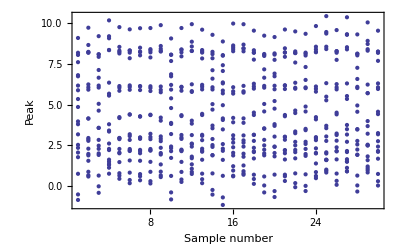

```mathematica
ListPlot[allAgainstRawSampleNumber,Frame->{True,True,False,False},FrameLabel->{"Sample number","Peak"}]
```

### Data plotted against correct peak correspondence

Look at scatter plot to see if I see any structure when all are plotted against one peak

It looks like we have (roughly) lines.  So, a first order predictor based on peak position could be linear.  Choose a one peak in the reference spectrum.  Then choose another

```mathematica
allAgainstFirst=Flatten[Map[Function[sample,With[{f=First[sample]},
Map[{f,#}&,Rest[sample]]]],pos],1];
```

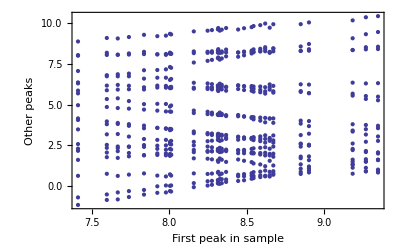

```mathematica
ListPlot[allAgainstFirst,Frame->{True,True,False,False},FrameLabel->{"First peak in sample","Other peaks"}]
```

### Data plotted against random peak correspondence

Compare that when each is paired with a random element from the same sample

```mathematica
allAgainstRandom=Flatten[Map[Function[rawSample,With[{sample=RandomSample[rawSample]},With[{f=First[sample]},
Map[{f,#}&,Rest[sample]]]]],pos],1];
```

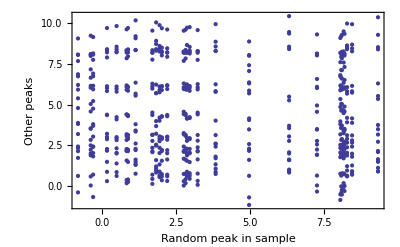

```mathematica
ListPlot[allAgainstRandom,Frame->{True,True,False,False},FrameLabel->{"Random peak in sample","Other peaks"}]
```

### Subtracting known peak

I'm going to investigate what happens when you subtract the first peak and then order by sample number - is the increase in order visible/detectable?

```mathematica
posAllMinusFirst=Map[Function[sample,With[{f=First[sample]},
Map[#-f&,sample]]],pos];
```

```mathematica
posAllMinusFirstAgainstRawSampleNumber=Flatten[MapThread[Function[{sample,sampleNumber},Map[{sampleNumber,#}&,sample]],{posAllMinusFirst,Range[Length[posAllMinusFirst]]}],1];
```

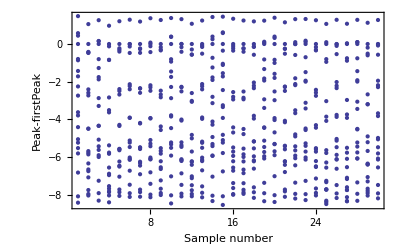

```mathematica
ListPlot[posAllMinusFirstAgainstRawSampleNumber,Frame->{True,True,False,False},FrameLabel->{"Sample number","Peak-firstPeak"}]
```

For comparison, here is the raw data

```mathematica
ListPlot[allAgainstRawSampleNumber,Frame->{True,True,False,False},FrameLabel->{"Sample number","Peak"}]
```

-Graphics-

### Plot sorted by position of first peak in list (to match diagram from paper)

```mathematica
rankOrdering[l_List,numElts_Integer,predicate_Function]:=Map[#[[2]]&,Sort[Thread[{Ordering[l,numElts,predicate],Range[Length[pos]]}]]]
```

```mathematica
rankPos=With[{rank=rankOrdering[pos,Length[pos],First[#1]<First[#2]&]},
MapThread[{#1,#2}&,{pos,rank}]];
```

```mathematica
allAgainstRank=	Flatten[Map[Function[sample,With[{r=sample[[2]],data=sample[[1]]},
Map[{#,r}&,data]]],rankPos],1];
```

```mathematica
firstAgainstRank=Map[{First[#[[1]]],#[[2]]}&,rankPos];
```

```mathematica
ListPlot[{allAgainstRank,firstAgainstRank},PlotStyle->{Red,Green},Frame->{True,True,False,False},FrameLabel->{"Peak position","Sample rank sorted by first generated peak"}]
```

-Graphics-

## 4 April 2011 Monday

### Implement beam search - description

I am going to try implementing the beam search idea with the following limitations: # peaks is same throughout and every peak is detected every time.

#### Variables

There will be a couple of variables:

initialPeakPositions: 2d array of the initial permutation of peaks: initialPeakPositions[[sample,peak]]  locations are given in ppm

beam: list of candidates with their current evaluation, sorted by evaluation

beamSize: number of candidates that will be in the beam at the start of each iteration

newCandidates: list of every possible candidate with one inversion different from a candidate in the initial beam

#### Types

candidate: each candidate is a list of permutations, one permutation per sample.  Each candidate is a potential solution.  If it is a correct solution, when each permutation is applied to the appropriate sample in initialPeakPositions, the first entries should correspond, the second entries should correspond, etc.

evaluation: an evaluation (evaluation[numEigenvalues,percentVarianceExplained] is better if there are fewer eigenvalues, but if the number of eigenvalues are equal, it is better if there is more variance explained by those eigenvalues.  This should be expanded into some notion of the compactness of the representation.

#### Functions

evaluate[candidate, initialPositions, pctVar]: applies the candidate to the given positions then calculates a PCA choosing enough eigenvectors to account for pctVar of the variance.  The evaluation returned gives the number of such eigenvectors and the proportion of the variance explained by them

isBetter[evaluation1,evaluation2]: returns true if evaluation1 is better than evaluation 2.

beamCorrespondence[peakPositions, beamSize, pctVar]: returns a candidate that gives the best correspondence found for the given peak positions

childCandidates[candidate, sampleIndex]: returns a list of all candidates that can be generated by swapping individual peaks in the sample at sampleIndex in the given candidate

applyCandidate[candidate, initialPositions]: applies the given candidate to the given list of initial positions, returning a permuted list of peak positions

### Code

```mathematica
childCandidates[candidate_List,sampleIndex_Integer]:=
With[{swaps=Append[Union[Select[Map[Sort,Tuples[Range[Length[candidate[[sampleIndex]] ] ],2]],#[[1]]≠#[[2]]&]],{1,1}],
(*TODO: Change swapped and newCandidate to use ReplacePart*)
swapped=Function[{permutation,swap},Table[Which[
i==swap[[1]],permutation[[swap[[2]]]],
i==swap[[2]],permutation[[swap[[1]]]],
True,permutation[[i]] ],{i,Length[permutation]}
]]},
With[{newCandidate=Function[swap,Table[If[i==sampleIndex,swapped[candidate[[i]],swap],candidate[[i]]],{i,Length[candidate]}]]},
Map[newCandidate,swaps]
]]
```

```mathematica
isBetter[ev1_evaluation, ev2_evaluation] := ev1[[1]] < ev2[[1]] || (ev1[[1]] == ev2[[1]] && ev1[[2]] > ev2[[2]])
```

```mathematica
applyCandidate[candidate_List, initialPositions_List]:=MapThread[#2[[#1]]&,{candidate,initialPositions}]
```

```mathematica
evaluate[candidate_List, initialPositions_List, pctVar_]/;NumberQ[pctVar]:=With[{permuted=applyCandidate[candidate,initialPositions]},
With[{varForEig=Normalize[Eigenvalues[Covariance[permuted]],Total]},
With[{cumVar=Accumulate[varForEig]},
With[{satisfiesPercent=First[First[Position[cumVar,x_/;x≥pctVar]]]},
evaluation[satisfiesPercent,cumVar[[satisfiesPercent]]]
]]]]
```

```mathematica
beamCorrespondence[peakPositions_List, beamSize_,pctVar_]/;(NumberQ[beamSize]&&NumberQ[pctVar]&&pctVar≥0&&pctVar≤1):=
With[{idPermutation=Table[Range[Dimensions[peakPositions][[2]]],{Length[peakPositions]}],
numSamples=Length[peakPositions],
numPeaks=Dimensions[peakPositions][[2]]},
With[{newBeam=Function[{oldBeam,sampleIndexToModify},
With[{children=Flatten[Map[childCandidates[#,sampleIndexToModify]&,oldBeam],1]},
With[{evaluated=Map[{#,evaluate[#,peakPositions,pctVar]}&,children]},
With[{sorted=Map[First,Sort[evaluated,isBetter[#1[[2]],#2[[2]]]&]]},
Take[sorted,beamSize]
]]]]},
With[{doIteration=Function[beam,Fold[newBeam,beam,Range[numSamples]]
]},
FixedPoint[doIteration, {idPermutation}][[1]]
]]]
```

#### Simple bench test

```mathematica
(*Note that the following could do just one inversion if it inverted the second sample first*)
```

```mathematica
beamCorrespondence[{{1,2},{2.21,1.15},{3.01,6.05}},1,9/10]
```

{{{2,1},{1,2},{2,1}}}

```mathematica
childCandidates[{{1,2},{1,2},{1,2}},1]
```

{{{2,1},{1,2},{1,2}},{{1,2},{1,2},{1,2}}}

```mathematica
idCandidate=Table[Range[20],{30}];
```

```mathematica
appliedIDCandidate=applyCandidate[idCandidate,pos];
```

```mathematica
pos==appliedIDCandidate
```

True

```mathematica
posEvaluation=evaluate[idCandidate,pos,9/10]
```

evaluation[1,0.940709]

```mathematica
(*Note that this next one uses the definition of permutedPos from the experiment looking at what happens to the eigenvalues when the values in the matrix are swapped*)
```

```mathematica
permutedPosEvaluation=evaluate[idCandidate,permutedPos,9/10]
```

evaluation[2,0.969265]

```mathematica
isBetter[posEvaluation,permutedPosEvaluation]
```

True

```mathematica
isBetter[permutedPosEvaluation,posEvaluation]
```

False

```mathematica
isBetter[posEvaluation,posEvaluation]
```

False

```mathematica
childCandidates[{{1,2},{3,4}},2]
```

{{{1,2},{4,3}},{{1,2},{3,4}}}

```mathematica
childCandidates[{{1,2,3},{3,4}},1]
```

{{{2,1,3},{3,4}},{{3,2,1},{3,4}},{{1,3,2},{3,4}},{{1,2,3},{3,4}}}

#### Code for permuted items eigenvalue test

```mathematica
meanCenterSamples[samples_List]:=With[{means=Mean[samples]},Map[#-means&,samples]]
```

```mathematica
adjustedRSquareds::usage="adjustedRSquareds[rsquareds, sampleSize] Given a list of R^2 values for each potential variable in a PCA model and the sample size from which the model was derived, uses the formula for adjusted R^2 from Wikipedia to calculate an estimate of the variance explained for the composite model that accounts for the size of the model.";
```

```mathematica
adjustedRSquareds[rsquareds_List,sampleSize_Integer]:=With[{cumRSq=Accumulate[rsquareds]},MapThread[Function[{rsq,p},1-((1-rsq)(sampleSize-1)/(sampleSize-p-1))],{cumRSq,Range[Length[rsquareds]]}]]
```

### See what happens to eigenvalue list when items are permuted

```mathematica
permutedPos=pos;
```

```mathematica
{permutedPos[[1,1]],permutedPos[[1,2]]}={permutedPos[[1,2]],permutedPos[[1,1]]}
```

{1.79079,8.54244}

```mathematica
{permutedPos[[1,1]],permutedPos[[1,2]]}
```

{1.79079,8.54244}

```mathematica
{pos[[1,1]],pos[[1,2]]}
```

{8.54244,1.79079}

```mathematica
MatrixRank[meanCenterSamples[permutedPos]]
```

4

p2pos is permutedPermutedPos (permute a second element)

```mathematica
p2pos=permutedPos;
```

```mathematica
{p2pos[[2,3]],p2pos[[2,5]]}={p2pos[[2,5]],p2pos[[2,3]]};
```

```mathematica
MatrixRank[meanCenterSamples[p2pos]]
```

5

```mathematica
p2posRSquareds=Normalize[#^2&/@SingularValueList[meanCenterSamples[p2pos]],Total]
```

{0.634855,0.319313,0.025804,0.0142224,0.00580569}

```mathematica
Normalize[Eigenvalues[Covariance[meanCenterSamples[p2pos]]],Total] (*Verify that the singular values of the mean-centered matrix are indeed the square roots of the eigenvalues*)
```

{0.634855,0.319313,0.025804,0.0142224,0.00580569,-1.37986×10^-16,7.73308×10^-17,-7.33128×10^-17,6.63941×10^-17,-4.79549×10^-17,-2.69968×10^-17,2.58742×10^-17,1.2538×10^-17,-1.23165×10^-17,-6.76716×10^-18,4.70851×10^-18,-3.39183×10^-18,-1.97652×10^-18,1.34887×10^-18,3.48221×10^-19}

```mathematica
Accumulate[p2posRSquareds]
```

{0.634855,0.954168,0.979972,0.994194,1.}

```mathematica
adjustedRSquareds[p2posRSquareds,Length[p2pos]]
```

{0.621814,0.950773,0.977661,0.993265,1.}

```mathematica
permutedPosRSquareds=Normalize[#^2&/@SingularValueList[meanCenterSamples[permutedPos]],Total]
```

{0.645185,0.32408,0.0221624,0.00857246}

```mathematica
Accumulate[permutedPosRSquareds]
```

{0.645185,0.969265,0.991428,1.}

```mathematica
adjustedRSquareds[permutedPosRSquareds,Length[permutedPos]]
```

{0.632513,0.966988,0.990438,1.}

```mathematica
Normalize[Eigenvalues[Covariance[permutedPos]],Total]
```

{0.645185,0.32408,0.0221624,0.00857246,9.51846×10^-17,-7.9391×10^-17,-5.50015×10^-17,2.76457×10^-17,-2.75428×10^-17,-2.16227×10^-17,1.8312×10^-17,-1.41181×10^-17,-9.35058×10^-18,7.33525×10^-18,-6.33149×10^-18,4.10511×10^-18,-3.34419×10^-18,2.53761×10^-18,8.01315×10^-19,1.95031×10^-19}

```mathematica
MatrixRank[Covariance[pos]]
```

3

```mathematica
posRSquareds=Normalize[#^2&/@SingularValueList[meanCenterSamples[pos]],Total]
```

{0.940709,0.0477953,0.0114957}

```mathematica
Accumulate[posRSquareds]
```

{0.940709,0.988504,1.}

## 5 April 2011 Tuesday

### Write code for generating a set of peaks and the permutation that would return it to the original

#### Peak generation code

```mathematica
randomPeaksAndPermutation::usage="randomPeaksAndPermutation[numPeaks,numSamples,factorStdDev,noiseStdDev,peakResponseStdDev,peakRange] 

Returns a list of rules {\"peaks\"→...,\"permutation\"→...}.

\"peaks\" gives a list of samples, each sample is a list of peaks sorted by their location.

\"permutation\" gives a list of permutations that, when applied to the corresponding sample, will make the i^th position in that sample contain the position of the i^th peak.  Thus, after applying all the permutations, the corresponding positions in the sample will contain corresponding peaks.

numPeaks and numSamples determine how many peaks and samples will be generated

Each sample has a number of latent factors s_j.  Each peak has the same number of latent response variables a_i.  Each peak also has a base location k_i.  The latent factors are selected from a multidimensional Gaussian with mean 0 and standard deviations given by factorStdDev.  Similarly the responses are selected from a Gaussian with mean 0 and standard deviations in peakResponseStdDev.  The peak means are selected independently from a uniform distribution over peakRange.

The i^th peak in the j^th sample is given a location:
δ_ij=k_i+a_i·s_j+ξ_ij

Where ξ_ij is a normally distributed random variable with mean 0 and standard deviation noiseStdDev.";
```

```mathematica
randomPeaksAndPermutation[numPeaks_Integer,numSamples_Integer,factorStdDev_List,noiseStdDev_,peakResponseStdDev_List,peakRange_List]/;Length[factorStdDev]==Length[peakResponseStdDev]&&NumberQ[noiseStdDev]&&noiseStdDev>0&&Length[peakRange]==2:=
With[{
s=Table[factorStdDev RandomReal[NormalDistribution[0,1],Length[factorStdDev]],{numSamples}],
a=Table[peakResponseStdDev RandomReal[NormalDistribution[0,1],Length[peakResponseStdDev]],{numPeaks}],
k=RandomReal[peakRange,numPeaks]},
With[{rawPos=Map[Function[sj,MapThread[Function[{ai,ki},ki+Dot[ai, sj]+RandomReal[NormalDistribution[0,noiseStdDev]]],{a,k}]],s]},
With[{sortOrdering=Map[Ordering,rawPos],
sortedPos=Map[Sort,rawPos]},
With[{unsortOrdering=Map[Ordering,sortOrdering]},
{"peaks"->sortedPos,"permutation"->unsortOrdering}
]]]]
```

#### Peak plotting code

```mathematica
asPeakPlotTuples::usage ="asPeakPlotTuples[peaks]
Returns a list of two lists, the first is a list of pairs of the peak locations in each sample plotted against the first peak location in that sample and the second is the first point in each sample plotted against itself.  If fed to ListPlot, it will show the ordering obtained by accounting for the variation in the first peak.";
```

```mathematica
asPeakPlotTuples[peaks_List]:=
With[{firsts=Map[First,peaks]},
With[{pairs=Flatten[MapThread[Function[{sample,first},Map[{#,first}&,sample]],{peaks,firsts}],1]},
{pairs,Map[{#,#}&,firsts]}]]
```

```mathematica
asSortedPlotTuples::usage ="asSortedPlotTuples[peaks]
Returns a list of two lists, the first is a list of pairs of the peak locations in each sample plotted against the sample number in that sample and the second is the first point in each sample plotted against the sample.  The samples are sorted according to the location of the location of the first peak.  

If fed to ListPlot, it will show the ordering obtained by accounting for the variation in the first peak as would be obtained by sorting according to one peak's location.";
```

```mathematica
asSortedPlotTuples[unsortedPeaks_List]:=
With[{sortedPeaks=Sort[unsortedPeaks,First[#1]<First[#2]&]},
With[{listOfPairs=MapThread[Function[{sample,sampleNum},Map[{#,sampleNum}&,sample]],{sortedPeaks,Range[Length[sortedPeaks]]}]},
{Flatten[listOfPairs,1],Map[First,listOfPairs]}
]]
```

#### Peak plotting code usage examples

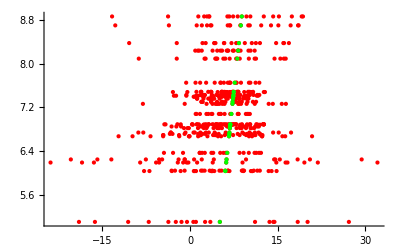

```mathematica
With[{raw=randomPeaksAndPermutation[20,30,{0.7,0.5,0.2},0.2,{10,1,1},{0,11}]},
With[{pks="peaks"/.raw,perm="permutation"/.raw},
ListPlot[asPeakPlotTuples[applyCandidate[perm,pks]],PlotStyle->{Red,Green}]
]]
```

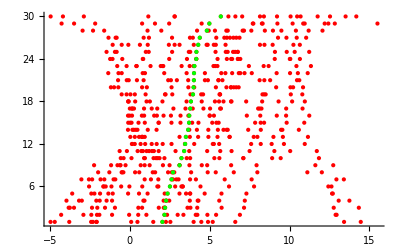

```mathematica
With[{raw=randomPeaksAndPermutation[20,30,{1,1,0.1},0.1,{3,0.5,1},{0,11}]},
With[{pks="peaks"/.raw,perm="permutation"/.raw},
ListPlot[asSortedPlotTuples[applyCandidate[perm,pks]],PlotStyle->{Red,Green}]
]]
```

### Write code for determining the % error between an ideal permutation and a calculated one

Since we only care about correspondence not the actual ordering in which the peaks were originally generated, we can sort the two correspondences based on their first permutation.

#### Difference code

```mathematica
fracDifferent::usage="fracDifferent[perm1,perm2] 
Returns the fraction of correspondences that are different between the two permutations"
```

fracDifferent[perm1,perm2] 
Returns the fraction of correspondences that are different between the two permutations

```mathematica
fracDifferent[perm1_List,perm2_List]/;Dimensions[perm1]==Dimensions[perm2]&&Length[perm1]≥1:=
With[{o1=Ordering[perm1[[1]]],o2=Ordering[perm2[[1]]]},
With[{sortP1=Map[#[[o1]]&,perm1],sortP2=Map[#[[o2]]&,perm2]},
With[{numDiff=MapThread[HammingDistance,{sortP1,sortP2}]},
Total[numDiff]/(Times@@(Dimensions[perm1]))
]]]
```

#### Bench test difference code

Each test below should be true

```mathematica
And[
fracDifferent[{{1,2,3},{1,3,2},{3,2,1}},{{3,2,1},{2,3,1},{1,2,3}}]==0,
fracDifferent[{{1,2,3},{1,3,2},{3,2,1}},{{3,2,1},{1,2,3},{1,2,3}}]==1/3,
fracDifferent[{{1,2,3},{1,3,2},{3,2,1}},{{3,2,1},{3,2,1},{1,2,3}}]==2/9,
fracDifferent[{{1,2,3},{1,3,2},{3,2,1}},{{3,2,1},{3,2,1},{1,3,2}}]==4/9
]
```

True

### Test beam search algorithm accuracy using synthetic data - it fails

#### Test one randomly chosen test sample - doesn't produce good results

```mathematica
With[{raw=randomPeaksAndPermutation[5,5,{1,0.1,0.01},0.0001,{1,1,1},{0,11}]},
With[{peaks="peaks"/.raw,correctPerm="permutation"/.raw},
With[{beamPerm=beamCorrespondence[peaks,1,90/100]},
fracDifferent[correctPerm,beamPerm]
]]]
```

1/5

#### Look at raw data - the permutation found by the beam search has a better evaluation than the true model

```mathematica
oneTestRun=With[{raw=randomPeaksAndPermutation[5,5,{1,0.1,0.01},0.0001,{1,1,1},{0,11}]},
With[{peaks="peaks"/.raw,correctPerm="permutation"/.raw},
With[{beamPerm=beamCorrespondence[peaks,5,9999/10000]},
With[{oCorrect=Ordering[correctPerm[[1]]],oBeam=Ordering[beamPerm[[1]]]},
{"correct"->Map[#[[oCorrect]]&,correctPerm],"beam"->Map[#[[oBeam]]&,beamPerm],"peaks"->peaks,"error"->fracDifferent[correctPerm,beamPerm]}
]]]]
```

{correct→{{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5}},beam→{{1,2,3,4,5},{1,2,3,4,5},{1,5,3,4,2},{1,2,3,4,5},{1,5,3,4,2}},peaks→{{0.982303,3.63468,5.27682,7.31836,10.611},{1.09605,3.54101,5.11142,7.303,10.5128},{0.614794,3.96991,5.75573,7.35231,10.6706},{2.05887,2.34062,3.69852,7.16685,10.2326},{0.0335904,4.72263,6.62224,7.43858,10.85}},error→4/25}

```mathematica
pks="peaks"/.oneTestRun
```

{{0.982303,3.63468,5.27682,7.31836,10.611},{1.09605,3.54101,5.11142,7.303,10.5128},{0.614794,3.96991,5.75573,7.35231,10.6706},{2.05887,2.34062,3.69852,7.16685,10.2326},{0.0335904,4.72263,6.62224,7.43858,10.85}}

```mathematica
correct="correct"/.oneTestRun
```

{{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5}}

```mathematica
beam="beam"/.oneTestRun
```

{{1,2,3,4,5},{1,2,3,4,5},{1,5,3,4,2},{1,2,3,4,5},{1,5,3,4,2}}

```mathematica
evaluate[correct,pks,9999/10000]
```

evaluation[3,1.]

```mathematica
evaluate[beam,pks,9999/10000]
```

evaluation[2,0.999999]

## 7 April 2011 Thursday

### Theoretical background to cross-validation evaluation function

I want to try to come up with a routine that uses cross-validation to evaluate model fit.  One open question is whether to use the minimum or average value over all folds as the evaluation.

I spent several hours calculating to discover that (if samples are in columns) then the shift factors (s in the paper) are the columns of the transformed samples and the reaction factors are the columns of the PCA eigenvector matrix.  If X is the mean-centered data, we have X=ΑS where A=P^T=P^-1 where P is the matrix of eigenvectors of the covariance matrix 1/(n-1)X X^T.  This relationship still holds even if you grab only the most significant eigenvectors.

## 11-13 April 2011 Monday-Wednesday

Discuss and investigate different options for version control and hosting for the development of the metabolomics code.

## 14 April 2011 Thursday

### Install fresh ubuntu on bio-db

### Work on creating evaluation based on cross-validation

#### First attempt is to use the expectation maximization algorithm

The following is a direct translation from the paper (I didn't use the missing values formulation yet).  I can't get it to work

```mathematica
emPCA[y_List,numEigenvectors_Integer]:=With[
{eStep = Function[c,With[{ct=Transpose[c]},Inverse[ct.c].ct.y]],
mStep=Function[x,With[{xt=Transpose[x]},y.xt.Inverse[x.xt]]]},
With[{iteration=Function[c,mStep[eStep[c]]],
initialMatrix=
Table[RandomReal[{-1/(1+numEigenvectors),1/(1+numEigenvectors)},numEigenvectors],{Length[y]}]},
FixedPoint[iteration,initialMatrix]
]]
```

```mathematica
Dimensions[testPCAValues]
```

{10,3}

#### I can't get it to work because it doesn't

Here I demonstrate symbolically that the steps given in the paper will always yield the same estimate for c when there are two eigenvectors for a space of 2D points.  I, however, saw the same equations (with different letters) in another paper.  So, there must be something I am not understanding here.

```mathematica
y=Transpose[{{a,b},{k,d},{e,f},{l,m}}]
```

{{a,k,e,l},{b,d,f,m}}

```mathematica
c={{g,h},{i,j}}
```

{{g,h},{i,j}}

```mathematica
ct=Transpose[c]
```

{{g,i},{h,j}}

```mathematica
x=Inverse[ct.c].ct.y
```

{{a ((h (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)+(g (h^2+j^2))/(h^2 i^2-2 g h i j+g^2 j^2))+b ((j (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)+(i (h^2+j^2))/(h^2 i^2-2 g h i j+g^2 j^2)),d ((j (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)+(i (h^2+j^2))/(h^2 i^2-2 g h i j+g^2 j^2))+((h (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)+(g (h^2+j^2))/(h^2 i^2-2 g h i j+g^2 j^2)) k,e ((h (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)+(g (h^2+j^2))/(h^2 i^2-2 g h i j+g^2 j^2))+f ((j (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)+(i (h^2+j^2))/(h^2 i^2-2 g h i j+g^2 j^2)),((h (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)+(g (h^2+j^2))/(h^2 i^2-2 g h i j+g^2 j^2)) l+((j (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)+(i (h^2+j^2))/(h^2 i^2-2 g h i j+g^2 j^2)) m},{a ((h (g^2+i^2))/(h^2 i^2-2 g h i j+g^2 j^2)+(g (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2))+b (((g^2+i^2) j)/(h^2 i^2-2 g h i j+g^2 j^2)+(i (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)),d (((g^2+i^2) j)/(h^2 i^2-2 g h i j+g^2 j^2)+(i (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2))+((h (g^2+i^2))/(h^2 i^2-2 g h i j+g^2 j^2)+(g (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)) k,e ((h (g^2+i^2))/(h^2 i^2-2 g h i j+g^2 j^2)+(g (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2))+f (((g^2+i^2) j)/(h^2 i^2-2 g h i j+g^2 j^2)+(i (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)),((h (g^2+i^2))/(h^2 i^2-2 g h i j+g^2 j^2)+(g (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)) l+(((g^2+i^2) j)/(h^2 i^2-2 g h i j+g^2 j^2)+(i (-g h-i j))/(h^2 i^2-2 g h i j+g^2 j^2)) m}}

```mathematica
xt=Transpose[x];
```

```mathematica
cnew=Simplify[y.xt.Inverse[x.xt]]
```

{{g,h},{i,j}}

```mathematica
c=cnew
```

{{0.0300051,0.0431783,-0.0176582},{-0.149382,0.144852,0.226486},{-0.0168415,-0.221313,0.0661678}}

```mathematica
Clear[c,ct,cnew,x,xt,y]
```

#### Here is some old code I used to test my implementation and discover that it didn't work

```mathematica
testPCAValues=
With[{rotxy=RotationTransform[π/4,{{1,0,0},{0,1,0}}]},Table[rotxy[{1,5,2} RandomReal[NormalDistribution[0,1],3]],{10}]
];
```

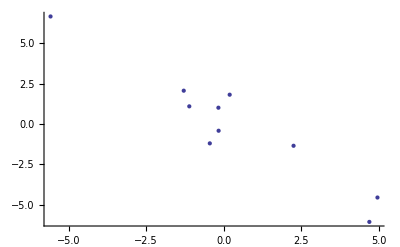

```mathematica
ListPlot[{First[#],#[[2]]}&/@testPCAValues]
```

```mathematica
Eigenvectors[Covariance[testPCAValues]]
```

{{0.645036,-0.760198,-0.0776321},{0.139212,0.0170112,0.990116},{0.751364,0.649468,-0.116801}}

```mathematica
emPCA[Transpose[testPCAValues],3]
```

{{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}},{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}},{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}},{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}},{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}},{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}},{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}},{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}},{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}},{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}},{{-0.106472,0.223833,-0.154553},{0.172309,0.245365,0.0395454},{-0.212689,-0.0734184,-0.140818}}}

## 15 April 2011 Friday

### Try a different approach to see if EM method works

Maybe it didn't work because my eigenvector matrix had all included.  It doesn't give the same result.  Whether it converges to something or not, I'll have to check in the sequel.

```mathematica
y=Transpose[{{a,b},{k,d},{e,f},{l,m}}]
```

{{a,k,e,l},{b,d,f,m}}

```mathematica
c={{g},{h}}
```

{{g},{h}}

```mathematica
ct=Transpose[c]
```

{{g,h}}

```mathematica
x=Inverse[ct.c].ct.y
```

{{(a g)/(g^2+h^2)+(b h)/(g^2+h^2),(d h)/(g^2+h^2)+(g k)/(g^2+h^2),(e g)/(g^2+h^2)+(f h)/(g^2+h^2),(g l)/(g^2+h^2)+(h m)/(g^2+h^2)}}

```mathematica
xt=Transpose[x];
```

```mathematica
cnew=Simplify[y.xt.Inverse[x.xt]]
```

{{((g^2+h^2) (a^2 g+e^2 g+a b h+e f h+d h k+g k^2+g l^2+h l m))/(a^2 g^2+e^2 g^2+2 a b g h+2 e f g h+b^2 h^2+d^2 h^2+f^2 h^2+2 d g h k+g^2 k^2+g^2 l^2+2 g h l m+h^2 m^2)},{((g^2+h^2) (a b g+e f g+b^2 h+d^2 h+f^2 h+d g k+g l m+h m^2))/(a^2 g^2+e^2 g^2+2 a b g h+2 e f g h+b^2 h^2+d^2 h^2+f^2 h^2+2 d g h k+g^2 k^2+g^2 l^2+2 g h l m+h^2 m^2)}}

```mathematica
c=cnew
```

{{((g^2+h^2) (a^2 g+e^2 g+a b h+e f h+d h k+g k^2+g l^2+h l m))/(a^2 g^2+e^2 g^2+2 a b g h+2 e f g h+b^2 h^2+d^2 h^2+f^2 h^2+2 d g h k+g^2 k^2+g^2 l^2+2 g h l m+h^2 m^2)},{((g^2+h^2) (a b g+e f g+b^2 h+d^2 h+f^2 h+d g k+g l m+h m^2))/(a^2 g^2+e^2 g^2+2 a b g h+2 e f g h+b^2 h^2+d^2 h^2+f^2 h^2+2 d g h k+g^2 k^2+g^2 l^2+2 g h l m+h^2 m^2)}}

```mathematica
Clear[c,ct,cnew,x,xt,y]
```

### I tried testing the EM method with fewer eigenvectors — it still doesn't work

```mathematica
testPCAValues=
With[{rotxy=RotationTransform[π/4,{{1,0,0},{0,1,0}}]},Table[rotxy[{1,5,2} RandomReal[NormalDistribution[0,1],3]],{20}]
];
```

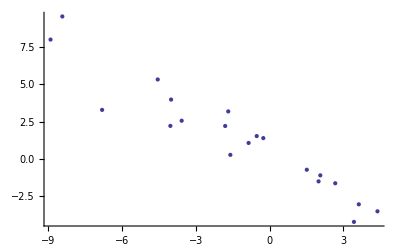

```mathematica
ListPlot[{First[#],#[[2]]}&/@testPCAValues]
```

```mathematica
Eigenvectors[Covariance[testPCAValues]]
```

{{-0.74049,0.672054,-0.00431347},{0.0236204,0.0324388,0.999195},{-0.671653,-0.739791,0.0398948}}

```mathematica
emPCA[Transpose[testPCAValues],1]
```

$Aborted

### Tried writing cross-validation without using missing values

This section also includes work I did on 19 April.  It relies on the description of PCA and SVD given in Practical approaches to principal component analysis in the presence of missing values by Ilin and Raiko.  That description is available in many places, but I wanted to note where I got it.

This section also includes bug fixes from 21 April and 22 April

```mathematica
wxDecompose::usage="wxDecompose[matrix,fracVar,minComponents]
Given a matrix whose columns have data and whose rows have zero mean, decomposes it into W and X so that W.X≈the original matrix and they have at least minComponents dimensions and sufficient dimensions to capture fracVar fraction of the variance 

See 19 April 2011 for how wx decomposition relates to sample and peak parameter sets

Returns {W,X}";
```

```mathematica
wxDecompose[matrix_List,fracVar_,minComponents_Integer:0]/;Length[Dimensions[matrix]]==2&&NumberQ[fracVar]:=
With[{svd=SingularValueDecomposition[matrix]},
With[{u=svd[[1]],Σ=svd[[2]], vt=ConjugateTranspose[svd[[3]]],numSing=Min[Dimensions[svd[[2]]]]},
With[{singularValues=Map[Σ[[#,#]]&,Range[numSing]]},
With[{fracVariances=Normalize[singularValues singularValues,Total]},
With[{cumulativeVars=Accumulate[fracVariances]},
With[{componentsForFracvar=First[First[Position[cumulativeVars,x_/;x≥fracVar,1]]]},
With[{componentsRequired=Max[minComponents,componentsForFracvar]},
With[{w=Transpose[Transpose[u][[Range[componentsRequired]]]],x=(Σ.vt)[[Range[componentsRequired]]]},
{w,x}
]]]]]]]]
```

```mathematica
reactionParameters::usage="reactionParameters[positions,excludedSamples,fracVar,minComponents]
Calculates the reaction parameters for each peak using SVD based PCA given a set of corresponding peak positions.  Samples at indices given by excludedSamples are not used to create the estimatereactionParameters

positions is an array of dimensions samples×peaks

Returns {means,reactionCoefficients} where means is a 1×peaks array and reactionCoefficients is a peaks×d array where d is the number of components needed to get fracVar fraction of the variance or minComponents, whichever is larger";
```

```mathematica
reactionParameters[positions_List, excludedSamples_List,fracVar_,minComponents_Integer:0]/;NumberQ[fracVar]:=
With[{includedSamples=Complement[Range[Length[positions]],excludedSamples]},
With[{editedPositions=positions[[includedSamples]]},
With[{means=Mean[editedPositions]},
With[{meanCenteredPos=Map[#-means&,editedPositions]},
With[{wxd=wxDecompose[Transpose[meanCenteredPos],fracVar,minComponents]},
With[{w=wxd[[1]],x=wxd[[2]]},
{means, w}
]]]]]]
```

```mathematica
sampleParameters::usage="sampleParameters[positions,excludedPeaks,fracVar,minComponents]
Calculates the reaction parameters for each peak using SVD based PCA given a set of corresponding peak positions.  peaks at indices given by excludedPeaks are not used to create the estimate

positions is an array of dimensions samples×peaks

Returns sampleCoefficients, a d×samples array where d is the number of components needed to get fracVar fraction of the variance or minComponents, whichever is larger";
```

```mathematica
sampleParameters[positions_List, excludedPeaks_List,fracVar_,minComponents_Integer:0]/;NumberQ[fracVar]:=
With[{includedPeaks=Complement[Range[Dimensions[positions][[2]]],excludedPeaks]},
With[{editedPositions=Transpose[Transpose[positions][[includedPeaks]]]},
With[{means=Mean[editedPositions]},
With[{meanCenteredPos=Map[#-means&,editedPositions]},
With[{wxd=wxDecompose[Transpose[meanCenteredPos],fracVar,minComponents]},
With[{w=wxd[[1]],x=wxd[[2]]},
x
]]]]]]
```

```mathematica
evaluationExcludingData::usage="estimationError[positions,testSamples,testPeaks,fracVar]
Returns an evaluation object from estimating the testPeaks peaks in the testSamples samples using the data from the rest of the corresponding peak positions and the hough-transform linear model - in this case, gives negative root sum of squared error (rather than variance accounted for) and the number of dimensions required to get it

LIMITATION: does not handle the case where the number of principal components in one direction is greater than the number of training variables in the other direction (and thus greater than the maximum number of variables the other can supply) -- TODO: need to fix this
";
```

```mathematica
evaluationExcludingData[positions_List, testSamples_List, testPeaks_List, fracVar_]/;NumberQ[fracVar]:=
Module[{
sampCoeff=sampleParameters[positions,testPeaks,fracVar],
reactCoeff=reactionParameters[positions,testSamples,fracVar]},
With[{reactCompNeeded=Dimensions[reactCoeff[[2]]][[2]],sampCompNeeded=Length[sampCoeff]},
reactCoeff=If[reactCompNeeded<sampCompNeeded,reactionParameters[positions,testSamples,fracVar,sampCompNeeded],reactCoeff];
sampCoeff=If[sampCompNeeded<reactCompNeeded,sampleParameters[positions,testPeaks,fracVar,reactCompNeeded],sampCoeff];
With[{estimatedPositions=Map[#+First[reactCoeff]&,Transpose[reactCoeff[[2]].sampCoeff]]},
With[{errors=positions-estimatedPositions,prinCompNeeded=Max[reactCompNeeded,sampCompNeeded]},
With[{testErrors=Transpose[Transpose[errors[[testSamples]]][[testPeaks]]]},
evaluation[prinCompNeeded,-Norm[testErrors,"Frobenius"]]
]]]]]
```

## 18 April 2011 Monday

### Investigate using techniques from compressed sampling for peak matching

#### The technique

Compressed sampling reconstructs a sparse coefficient matrix from a random sample of a signal.  Let f be a big vector containing the signal.  We assume that there is a basis in which f  is sparse, that is, if β is a matrix of basis vectors and c is a sparse matrix of coefficients.

f=β c

Further, if ϕ is a sampling operator matrix (could be a subset of the identity matrix, for a random sample, or could be another matrix involving sampling averages of several function values) we can construct b, a sample of f, by writing

b=ϕ f

Note that ϕ has to carry a significant amount of information.  For example, if all the entries in ϕ are the same, then each sample adds no new information, and the problem cannot be solved.  If the samples all come from the beginning of the signal, then certain components may not be able to be reconstructed (this will depend on how the information about the signal is spread over the sparse basis vectors).

The reconstruction takes place by solving for

A x = b where A = ϕ β, that is, where A is a sample of the basis vectors.

Then we approximate f by f ≈ β x.

Since the sampling matrix takes a very small subset of the original vectors, the system of equations, A x = b is underdetermined.  The magic of the compressed reconstruction is to assume that c is sparse.  Then it turns out that (1) maximizing sparsity usually gives a unique solution (2) that solution is highly likely to be the correct one (3) you can maximize sparsity by minimizing the L_1 norm of x with the linear constraints given by A and b.

#### Why I was interested

I saw a linear combination involving a sparse matrix and thought such a linear combination resembles what we are doing.  In particular a permutation matrix is a sparse matrix and the β matrix bears a resemblance to the linear model

#### Why I don't think it will work now

The technique requires knowing a sampling matrix and the matrix of basis vectors, or, at least their product.  This doesn't seem to translate well to our problem where we'd have to a priori know the linear model (peak responses and sample parameters) which would take the place of the basis vectors.

#### Potential profit

The idea of being able to solve for the permutation by minimizing the L_1 norm of a particular matrix with constraints determined by the peak samples is still intriguing to me.  I have a feeling I might be able to make something out of this.

### Meet with Dan and Paul

We discussed moving from sending matlab scripts around to sending platform-dependent executables.

The scientists have trouble finding which thing they should click on to accomplish their tasks amid the myriad of .m files.

In order to do the deployment, we'll have VMs of Linux, Windows, and OS X running.  We run the Matlab deployment in each of these.

Further, for our development of the website code, we'll distribute a VM containing an ubuntu system on which rails etc has been already configured.  Then the current code can be downloaded into this VM and developers can run it within the VM, all having the same setup as the final deployment platform.  We may just run the final deployment as another instance of this VM.  But not sure if it would be too slow.  The benefits of VMWare and VirtualBox were discussed and it seems (from a cursory inspection of benchmarks) that they are the same.  Dan, however, has a bad experience running a game-server on VirtualBox, but it worked better under VMWare.

In order to run the deployment virtual machines on the development server, we decided to install ubuntu desktop (since virtualbox apparently can't run without an x server).  I'm not sure about that, but I don't do system administration.

## 19 April 2011 Tuesday

### Cross-validation evaluation fit

#### Completed existing code

I modified the code for cross validation under April 15^th.  Made it functional

#### Bench Tested

##### wxDecompose

Combining gives back initial matrix

Check that combining the decomposition gives us back our initial matrix

```mathematica
{w,x} =With[{p=Transpose[{{1,2,3,4},3{1,2,3,4},2{1,2,3,4}}]},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
wxDecompose[mc,1]
]]]
```

{{{-3/(2 √5)},{-1/(2 √5)},{1/(2 √5)},{3/(2 √5)}},{{√5,3 √5,2 √5}}}

Here is the original matrix

```mathematica
With[{p=Transpose[{{1,2,3,4},3{1,2,3,4},2{1,2,3,4}}]},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
mc
]]]
```

{{-3/2,-9/2,-3},{-1/2,-3/2,-1},{1/2,3/2,1},{3/2,9/2,3}}

Here is w.x

```mathematica
w.x
```

{{-3/2,-9/2,-3},{-1/2,-3/2,-1},{1/2,3/2,1},{3/2,9/2,3}}

It is the eigenvectors of mc (the mean centered matrix) times its transpose.

```mathematica
With[{p=Transpose[{{1,2,3,4},3{1,2,3,4},2{1,2,3,4}}]},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
Normalize/@Eigenvectors[mc.Transpose[mc]]
]]]
```

{{-3/(2 √5),-1/(2 √5),1/(2 √5),3/(2 √5)},{1/(√2),0,0,1/(√2)},{1/(√10),0,3/(√10),0},{-1/(√10),3/(√10),0,0}}

```mathematica
With[{p={{1,2,3,4},3{1,2,3,4},2{1,2,3,4}}},Covariance[p]]
```

{{1,2,3,4},{2,4,6,8},{3,6,9,12},{4,8,12,16}}

```mathematica
With[{p={{1,2,3,4},3{1,2,3,4},2{1,2,3,4}}},Covariance[Transpose[p]]]
```

{{5/3,5,10/3},{5,15,10},{10/3,10,20/3}}

```mathematica
With[{p=Transpose[{{1,2,3,4},3{1,2,3,4},2{1,2,3,4}}]},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
mc.Transpose[mc]
]]]
```

{{63/2,21/2,-21/2,-63/2},{21/2,7/2,-7/2,-21/2},{-21/2,-7/2,7/2,21/2},{-63/2,-21/2,21/2,63/2}}

```mathematica
With[{p=Transpose[{{1,2,3,4},3{1,2,3,4},2{1,2,3,4}}]},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
Transpose[mc].mc
]]]
```

{{5,15,10},{15,45,30},{10,30,20}}

Try to recover w and x from w.x

Looking at it later, this is a fool's errand - you need to make sure that the maximum variance is along the axes before you can recover the matrices

```mathematica
Normalize[{2, 0, 2, -1}]
```

{2/3,0,2/3,-1/3}

```mathematica
x=.
```

Find some nice unit vectors

```mathematica
rational4DUnitVectorsFromRange[maxElt_Integer]:=With[{r=maxElt},
Normalize/@With[{range=Range[2 r+1]-r-1},Select[Tuples[{range,range,range,range}],Function[{l},With[{len=Norm[l]},len ≠ 0&&And@@Map[Element[#/len,Rationals]&,l]]]]
]]
```

```mathematica
Sort[DeleteDuplicates[rational4DUnitVectorsFromRange[7],Sort[Abs[#1]]==Sort[Abs[#2]]&],Max[Denominator/@#1]<Max[Denominator/@#2]&]
```

{{-1,0,0,0},{-1/2,-1/2,-1/2,-1/2},{-2/3,-2/3,-1/3,0},{-4/5,-2/5,-2/5,-1/5},{-4/5,-3/5,0,0},{-5/6,-1/2,-1/6,-1/6},{-4/7,-4/7,-4/7,-1/7},{-5/7,-4/7,-2/7,-2/7},{-6/7,-3/7,-2/7,0},{-2/3,-5/9,-4/9,-2/9},{-7/9,-4/9,-4/9,0},{-7/10,-1/2,-1/2,-1/10},{-7/10,-7/10,-1/10,-1/10},{-7/11,-6/11,-6/11,0}}

It looks like any orthogonal basis w with only two basis vectors that will produce a zero mean requires that the two rows of the x vector be linearly dependent.  (Though I only tried two different w1 vectors)

```mathematica
Simplify[With[{w1={-5/6,-1/2,-1/6,-1/6},w2={ea,eb,ec,ed}},Reduce[Mean[Transpose[{w1,w2}].{{aa,ab,ac,ad},{ba,bb,bc,bd}}]=={0,0,0,0}&&w1.w2==0]]]
```

5 ea+3 eb+ec+ed==0&&25 ad==6 bd (eb+2 (ec+ed))&&25 ac==6 bc (eb+2 (ec+ed))&&25 ab==6 bb (eb+2 (ec+ed))&&25 aa==6 ba (eb+2 (ec+ed))

So, I need to try a 3D basis

```mathematica
Simplify[With[{w1={-5/6,-1/2,-1/6,-1/6},w2={ea,eb,ec,ed},w3={fa,fb,fc,fd}},Reduce[Mean[Transpose[{w1,w2,w3}].{{aa,ab,ac,ad},{ba,bb,bc,bd},{ca,cb,cc,cd}}]=={0,0,0,0}&&w1.w2==0&&w1.w3==0&&w2.w3==0&&Norm[w3]≠0&&Norm[w2]≠0]]]
```

((eb≠0&&eb+9 ec==0&&eb+9 ed==0&&fb==0&&√((25 Abs[eb]^2+25 Abs[ec]^2+25 Abs[ed]^2+Abs[3 eb+ec+ed]^2) (25 Abs[fc]^2+25 Abs[fd]^2+Abs[fc+fd]^2))≠0)||(√((25 Abs[eb]^2+25 Abs[ec]^2+25 Abs[ed]^2+Abs[3 eb+ec+ed]^2) (25 Abs[fb]^2+25 Abs[fc]^2+25 Abs[fd]^2+Abs[3 fb+fc+fd]^2))≠0&&((3 eb+ec+26 ed==0&&((35 eb+3 ec) fb)/(3 (eb+9 ec))+fc==0&&eb+9 ec≠0)||((34 eb fb+3 ec fb+3 ed fb+3 eb fc+26 ec fc+ed fc)/(3 eb+ec+26 ed)+fd==0&&3 eb+ec+26 ed≠0))))&&5 fa+3 fb+fc+fd==0&&5 ea+3 eb+ec+ed==0&&5 ad==3 (bd (ea+eb+ec+ed)+cd (fa+fb+fc+fd))&&5 ac==3 (bc (ea+eb+ec+ed)+cc (fa+fb+fc+fd))&&5 ab==3 (bb (ea+eb+ec+ed)+cb (fa+fb+fc+fd))&&5 aa==3 (ba (ea+eb+ec+ed)+ca (fa+fb+fc+fd))

That looks more promising.  Substitue numbers and see how things simplify then substitute again until we get a tautology.

```mathematica
Simplify[With[{w1={-5/6,-1/2,-1/6,-1/6},w2={-10/13,1,1,-2/13},w3={1/5,-15/13,19/13,1}},Reduce[Mean[Transpose[{w1,w2,w3}].{42/325{ba+ca,bb+cb,bc+cc,bd+cd},1/5{ba,bb,bc,bd},1/7{ca,cb,cc,cd}}]=={0,0,0,0}&&w1.w2==0&&w1.w3==0&&w2.w3==0&&Norm[w3]≠0&&Norm[w2]≠0]]]
```

True

But when we make the vectors unit - there is a problem - b becomes a multiple of c, continuing anyway for now

```mathematica
With[{w1={-5/6,-1/2,-1/6,-1/6},w2={-5 √(2/221),√(13/34),√(13/34),-√(2/221)},w3={13/138,-25/46,95/138,65/138}},
With[{x2=1/5{ba,bb,bc,bd},x3=1/7{ca,cb,cc,cd}},
With[{x1=42/325(5x2+7x3)},
Reduce[Mean[Transpose[{w1,w2,w3}].{x1,x2,x3}]=={0,0,0,0}]
]]]
```

bd==(1241 cd)/(69 (-34+√442))&&bc==(1241 cc)/(69 (-34+√442))&&bb==(1241 cb)/(69 (-34+√442))&&ba==(1241 ca)/(69 (-34+√442))

```mathematica
With[{w1={-5/6,-1/2,-1/6,-1/6},w2={-10/13,1,1,-2/13},w3={1/5,-15/13,19/13,1}},
With[{x2=1/5{1,2,3,4},x3=1/7{1,3,3,1}},
With[{x1=42/325(5x2+7x3)},
{Evaluate[Transpose[{w1,w2,w3}]],Evaluate[{x1,x2,x3}]}
]]]
```

{{{-5/6,-10/13,1/5},{-1/2,1,-15/13},{-1/6,1,19/13},{-1/6,-2/13,1}},{{84/325,42/65,252/325,42/65},{1/5,2/5,3/5,4/5},{1/7,3/7,3/7,1/7}}}

Now, I can substitue my favorite numbers in for the b and c vectors and get my test data.

```mathematica
{testResultMc,testResultM,testResultPw,testResultPx}=Simplify[
With[{pw={{-5/6,-10/13,1/5},{-1/2,1,-15/13},{-1/6,1,19/13},{-1/6,-2/13,1}},px={{84/325,42/65,252/325,42/65},{1/5,2/5,3/5,4/5},{1/7,3/7,3/7,1/7}}},
With[{p=pw.px},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
{mc,m,pw,px}
]]]]]
```

{{{-31/91,-346/455,-93/91,-512/455},{-214/2275,-38/91,-642/2275,142/455},{64/175,418/455,192/175,82/91},{157/2275,118/455,471/2275,-8/91}},{0,0,0,0},{{-5/6,-10/13,1/5},{-1/2,1,-15/13},{-1/6,1,19/13},{-1/6,-2/13,1}},{{84/325,42/65,252/325,42/65},{1/5,2/5,3/5,4/5},{1/7,3/7,3/7,1/7}}}

```mathematica
Transpose[Normalize/@Transpose[testResultPw]]//N
```

{{-0.833333,-0.475651,0.0942029},{-0.5,0.618347,-0.543478},{-0.166667,0.618347,0.688406},{-0.166667,-0.0951303,0.471014}}

```mathematica
Normalize/@testResultPx//N
```

{{0.210819,0.527046,0.632456,0.527046},{0.182574,0.365148,0.547723,0.730297},{0.223607,0.67082,0.67082,0.223607}}

```mathematica
{w,x}= wxDecompose[testResultMc//N,1]
```

{{{0.69989,-0.30243},{0.0935089,0.849027},{-0.702206,-0.134908},{-0.0911933,-0.41169}},{{-0.51032,-1.24003,-1.53096,-1.38313},{-0.0545877,-0.355264,-0.163763,0.519916}}}

Maybe I have to have w=orthogonal unit vectors to get it back from the decomposition

```mathematica
rotated4DUnit[θ1_,θ2_,θ3_]:=With[{u1={1,0,0,0},u2={0,1,0,0},u3={0,0,1,0},u4={0,0,0,1}},
RotationTransform[θ1,{u2,u1}][
RotationTransform[θ2,{u3,u2}][
RotationTransform[θ3,{u4,u3}][u4
]]]]
```

```mathematica
Simplify[With[{w1={-5/6,-1/2,-1/6,-1/6},w2=rotated4DUnit[e1,e2,e3],w3=rotated4DUnit[f1,f2,f3]},Reduce[Mean[Transpose[{w1,w2,w3}].{{aa,ab,ac,ad},{ba,bb,bc,bd},{ca,cb,cc,cd}}]=={0,0,0,0}&&w1.w2==0&&w1.w3==0&&w2.w3==0]
]]
```

$Aborted

```mathematica
Simplify[With[{w1={0,0,0,1},w2={0,0,1,0},w3={0,1,0,0}},Reduce[Mean[Transpose[{w1,w2,w3}].{{aa,ab,ac,ad},{ba,bb,bc,bd},{ca,cb,cc,cd}}]=={0,0,0,0}&&w1.w2==0&&w1.w3==0&&w2.w3==0]
]]
```

ad+bd+cd==0&&ac+bc+cc==0&&ab+bb+cb==0&&aa+ba+ca==0

```mathematica
With[{w1={0,0,0,1},w2={0,0,1,0},w3={0,1,0,0}},Transpose[{w1,w2,w3}]
]
```

{{0,0,0},{0,0,1},{0,1,0},{1,0,0}}

```mathematica
{testResultMc,testResultM,testResultPw,testResultPx}=Simplify[
With[{pw={{0,0,0},{0,0,1},{0,1,0},{1,0,0}},px={{1,2,3,4},{-1,-1,-2,-2},{0,-1,-1,-2}}},
With[{p=pw.px},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
{mc,m,pw,px}
]]]]]
```

{{{0,0,0,0},{0,-1,-1,-2},{-1,-1,-2,-2},{1,2,3,4}},{0,0,0,0},{{0,0,0},{0,0,1},{0,1,0},{1,0,0}},{{1,2,3,4},{-1,-1,-2,-2},{0,-1,-1,-2}}}

```mathematica
{w,x}=Simplify[ wxDecompose[testResultMc,1]]
```

{{{0},{(-5125-920 √31)/(√(424124764+76175054 √31))},{-(3 (2243+403 √31))/(√(424124764+76175054 √31))},{(11854+2129 √31)/(√(424124764+76175054 √31))}},{{1/165 √(1669/3-18583/(6 √31)) (409+74 √31),1/55 √(1669/3-18583/(6 √31)) (262+47 √31),1/33 √(1669/3-18583/(6 √31)) (239+43 √31),1/55 √(6676/3-37166/(3 √31)) (262+47 √31)}}}

```mathematica
FullSimplify[w.x]
```

{{0,0,0,0},{-5/(2 √31),-1/2-2/(√31),-1/2-9/(2 √31),-1-4/(√31)},{-1/2-1/(2 √31),-1/2-7/(2 √31),-1-4/(√31),-1-7/(√31)},{1/2+3/(√31),1+11/(2 √31),3/2+17/(2 √31),2+11/(√31)}}

```mathematica
Eigensystem[testResultMc.Transpose[testResultMc]]
```

{{23+4 √31,23-4 √31,0,0},{{0,-47/4+1/4 (23+4 √31),43/4+1/4 (-23-4 √31),1},{0,-47/4+1/4 (23-4 √31),43/4+1/4 (-23+4 √31),1},{0,1,1,1},{1,0,0,0}}}

#### Earlier attempts at generating test data

```mathematica
{testResultMc,testResultM,testResultPw,testResultPx}=Simplify[
With[{pw={{0,2/(√21)},{2/3,√(3/7)},{-2/3,2/(√21)},{1/3,-2/(√21)}},px={{-4/5,-2/5,-2/5,1/5},{4/7,4/7,-4/7,-1/7}}},
With[{p=pw.px},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
{mc,m,pw,px}
]]]]]
```

{{{1/15+(√(3/7))/7,1/30+(√(3/7))/7,1/30-(√(3/7))/7,-1/60-(√(3/7))/28},{-7/15+1/(√21),-7/30+1/(√21),-7/30-1/(√21),7/60-1/(4 √21)},{3/5+(√(3/7))/7,3/10+(√(3/7))/7,3/10-(√(3/7))/7,-3/20-(√(3/7))/28},{-1/5-13/(7 √21),-1/10-13/(7 √21),-1/10+13/(7 √21),1/20+13/(28 √21)}},{-1/15+5/(7 √21),-1/30+5/(7 √21),-1/30-5/(7 √21),1/60-5/(28 √21)},{{0,2/(√21)},{2/3,√(3/7)},{-2/3,2/(√21)},{1/3,-2/(√21)}},{{-4/5,-2/5,-2/5,1/5},{4/7,4/7,-4/7,-1/7}}}

```mathematica
testResultPw//N
```

{{0.,0.436436},{0.666667,0.654654},{-0.666667,0.436436},{0.333333,-0.436436}}

```mathematica
testResultMc//N
```

{{0.160189,0.126855,-0.0601886,-0.0400472},{-0.248449,-0.0151154,-0.451551,0.0621122},{0.693522,0.393522,0.206478,-0.17338},{-0.605262,-0.505262,0.305262,0.151315}}

```mathematica
{w,x}= wxDecompose[testResultMc//N,1]
```

{{{-0.175154,-0.107135},{0.194271,-0.766008},{-0.69198,0.335173},{0.672863,0.537971}},{{-0.963485,-0.637437,-0.0146604,0.240871},{0.0799882,-0.141931,0.585768,-0.0199971}}}

```mathematica
{w,x}//N
```

{{{-0.175154},{0.194271},{-0.69198},{0.672863}},{{-0.963485,-0.637437,-0.0146604,0.240871}}}

```mathematica
w.x//N
```

{{0.227105,0.15422,-0.00844949,-0.0567763},{-0.256712,-0.174325,0.00955103,0.0641781},{0.710922,0.482765,-0.02645,-0.177731},{-0.681315,-0.46266,0.0253485,0.170329}}

### Explanation between PCA (or equiv. WX decomposition) and sample and peak parameter sets

PCA finds Y = W X + M where

Y is d × n

Data is in columns of Y

X is c × n

Weights for each eigenvector in the n^th sample are in the n^th row of x

W is d × c

Basis vectors for projected subspace (eigenvectors) are columns of W

M is d × n (n copies of bias vector)

d = number of dimensions per data point

n = number of data points

c = number of principal components

If Y=P^Twhere P is the peak position matrix, P is samples × peaks and Y is samples × peaks

Thus, d= peaks and n=samples

X = c × samples and W is peaks × c.

#### Crucial point

Y=P^T=W X+M

each column of X is a list of sample parameters

each row of W is a list of peak parameters

each row column of M is the same list of peak biases (potentially means)

### Mean-centering makes distributional assumptions

By subtracting the mean, from the peaks we implicitly look for the axis of most variation with respect to the mean.  Is that a good assumption?  Does it mean that the things driving the peak movements are varying around a known center?  This needs more thought.

## 21 April 2011 Thursday

### Bench tested wxDecompose

#### First, try to combine and get back the initial matrix using my fools-errand created initial vectors -- it didn't work

```mathematica
{testResultMc,testResultM,testResultPw,testResultPx}=Simplify[
With[{pw={{-5/6,-10/13,1/5},{-1/2,1,-15/13},{-1/6,1,19/13},{-1/6,-2/13,1}},px={{84/325,42/65,252/325,42/65},{1/5,2/5,3/5,4/5},{1/7,3/7,3/7,1/7}}},
With[{p=pw.px},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
{mc,m,pw,px}
]]]]]
```

{{{-31/91,-346/455,-93/91,-512/455},{-214/2275,-38/91,-642/2275,142/455},{64/175,418/455,192/175,82/91},{157/2275,118/455,471/2275,-8/91}},{0,0,0,0},{{-5/6,-10/13,1/5},{-1/2,1,-15/13},{-1/6,1,19/13},{-1/6,-2/13,1}},{{84/325,42/65,252/325,42/65},{1/5,2/5,3/5,4/5},{1/7,3/7,3/7,1/7}}}

```mathematica
{testResultW,testResultX}=wxDecompose[testResultMc,1]; N[{testResultW,testResultX}]
```

{{{-0.69989},{-0.0935089},{0.702206},{0.0911933}},{{0.51032,1.24003,1.53096,1.38313}}}

It doesn't work

```mathematica
testResultW.testResultX//N
```

{{-0.357168,-0.867882,-1.0715,-0.968037},{-0.0477195,-0.115953,-0.143158,-0.129335},{0.35835,0.870754,1.07505,0.971239},{0.0465378,0.113082,0.139613,0.126132}}

```mathematica
testResultMc//N
```

{{-0.340659,-0.76044,-1.02198,-1.12527},{-0.0940659,-0.417582,-0.282198,0.312088},{0.365714,0.918681,1.09714,0.901099},{0.069011,0.259341,0.207033,-0.0879121}}

The SVD does work.

```mathematica
{testResultU,testResultΣ,testResultV}=SingularValueDecomposition[testResultMc];
```

```mathematica
FullSimplify[testResultU.testResultΣ.Transpose[testResultV]]
```

{{-31/91,-346/455,-93/91,-512/455},{-214/2275,-38/91,-642/2275,142/455},{64/175,418/455,192/175,82/91},{157/2275,118/455,471/2275,-8/91}}

The problem is that I am only getting one component when I should get two (there are two non-zero singular values, so to get 100%(=1 as a fraction), I should be getting two components).

```mathematica
testResultΣ
```

{{1/455 √(6/5 (559079+√235738817841)),0,0,0},{0,1/455 √(6/5 (559079-√235738817841)),0,0},{0,0,0,0},{0,0,0,0}}

#### Fix bug from last test

##### Hand execute wxDecompose on the results to find out where it is getting only one

```mathematica
Min[Dimensions[testResultΣ]]
```

4

```mathematica
testResultSingularValues=Map[testResultΣ[[#,#]]&,Range[4]]
```

{1/455 √(6/5 (559079+√235738817841)),1/455 √(6/5 (559079-√235738817841)),0,0}

```mathematica
testResultFracVariances=FullSimplify[Normalize[testResultSingularValues testResultSingularValues,Total]]
```

{1/2+(√235738817841)/1118158,1/2-(√235738817841)/1118158,0,0}

```mathematica
testResultCumulativeVars=Accumulate[testResultFracVariances]
```

{1/2+(√235738817841)/1118158,1,1,1}

The bug is that the first element in the list of fractional variances is not an integer or a real but an expression, thus values of one or more are found in many different places within it -- need to restrict to the top level

```mathematica
testResultComponentsRequired=Position[testResultCumulativeVars,x_/;x≥1]
```

{{1,2,2,1},{1,2,2},{2},{3},{4}}

Restricted to the top level, produces the correct result

```mathematica
testResultComponentsRequired=First[First[Position[testResultCumulativeVars,x_/;x≥1,1]]]
```

2

#### Now repeat the first test on the fixed code

```mathematica
{testResultMc,testResultM,testResultPw,testResultPx}=Simplify[
With[{pw={{-5/6,-10/13,1/5},{-1/2,1,-15/13},{-1/6,1,19/13},{-1/6,-2/13,1}},px={{84/325,42/65,252/325,42/65},{1/5,2/5,3/5,4/5},{1/7,3/7,3/7,1/7}}},
With[{p=pw.px},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
{mc,m,pw,px}
]]]]]
```

{{{-31/91,-346/455,-93/91,-512/455},{-214/2275,-38/91,-642/2275,142/455},{64/175,418/455,192/175,82/91},{157/2275,118/455,471/2275,-8/91}},{0,0,0,0},{{-5/6,-10/13,1/5},{-1/2,1,-15/13},{-1/6,1,19/13},{-1/6,-2/13,1}},{{84/325,42/65,252/325,42/65},{1/5,2/5,3/5,4/5},{1/7,3/7,3/7,1/7}}}

```mathematica
{testResultW,testResultX}=wxDecompose[testResultMc,1]; N[{testResultW,testResultX}]
```

{{{-0.69989,-0.30243},{-0.0935089,0.849027},{0.702206,-0.134908},{0.0911933,-0.41169}},{{0.51032,1.24003,1.53096,1.38313},{-0.0545877,-0.355264,-0.163763,0.519916}}}

It works

```mathematica
FullSimplify[testResultW.testResultX]
```

{{-31/91,-346/455,-93/91,-512/455},{-214/2275,-38/91,-642/2275,142/455},{64/175,418/455,192/175,82/91},{157/2275,118/455,471/2275,-8/91}}

#### Test with eigenvector-transformed 4-Gaussian

I will generate a large dataset of zero-mean 4-d Gaussian points with maximum variance on the axes and multiply them by an orthogonal matrix and see if the orthogonal matrix is recovered

```mathematica
testResultGaussianPoints=Transpose[Table[Map[RandomReal[NormalDistribution[0,#]]&,{10,10,10,10}],{1000}]];
```

```mathematica
Precision[testResultGaussianPoints[[2,1]]]
```

MachinePrecision

To transform these, I will need a 4-d basis - so I need to choose a vector orthogonal to the ones I already have.  And make it a unit basis

```mathematica
Transpose[{{-5/6,-10/13,1/5},{-1/2,1,-15/13},{-1/6,1,19/13},{-1/6,-2/13,1}}]
```

{{-5/6,-1/2,-1/6,-1/6},{-10/13,1,1,-2/13},{1/5,-15/13,19/13,1}}

```mathematica
Normalize/@{{-5/6,-1/2,-1/6,-1/6},{-10/13,1,1,-2/13},{1/5,-15/13,19/13,1}}
```

{{-5/6,-1/2,-1/6,-1/6},{-5 √(2/221),√(13/34),√(13/34),-√(2/221)},{13/138,-25/46,95/138,65/138}}

```mathematica
Reduce[With[{v={aa,ab,ac,1}},And@@Map[v.#==0&,{{-5/6,-1/2,-1/6,-1/6},{-10/13,1,1,-2/13},{1/5,-15/13,19/13,1}}]],Reals]
```

ac==-494/1249&&ab==390/1249&&aa==-385/1249

```mathematica
testResultPwTransp=Simplify[Normalize/@{{-5/6,-1/2,-1/6,-1/6},{-10/13,1,1,-2/13},{1/5,-15/13,19/13,1},{-385/1249,390/1249,-494/1249,1}}]
```

{{-5/6,-1/2,-1/6,-1/6},{-5 √(2/221),√(13/34),√(13/34),-√(2/221)},{13/138,-25/46,95/138,65/138},{-385/(69 √442),(5 √(26/17))/23,-(19 √(26/17))/69,1249/(69 √442)}}

Verify that I do indeed have a unit, orthogonal basis

```mathematica
testResultPwTransp.Transpose[testResultPwTransp]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

Now perform the test

```mathematica
Timing[{testResultMc,testResultM,testResultPw,testResultPx}=Simplify[
With[{pw=Transpose[testResultPwTransp],px=testResultGaussianPoints},
With[{p=pw.px},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
{mc,m,pw,px}
]]]]];testResultPw//N]
```

{0.04,{{-0.833333,-0.475651,0.0942029,-0.2654},{-0.5,0.618347,-0.543478,0.268846},{-0.166667,0.618347,0.688406,-0.340539},{-0.166667,-0.0951303,0.471014,0.860998}}}

```mathematica
Timing[{testResultW,testResultX}=wxDecompose[testResultMc,1];]
```

{0.25,Null}

Surprisingly, I get only 3 components - due to rounding error?  (This happens even at precisions up to 512 bits)  I tried with exact numbers but even 20 Gaussian samples took more than 3 hours (at which point I gave up).  I gave up after half an hour for 5 samples with exact numbers.  I also tried 20 samples at a precision of 1048560 (that is about 3.5 million bits) and still came up with 3 components.

```mathematica
Dimensions/@{testResultW,testResultX}
```

{{4,3},{3,1000}}

The reconstruction is still very close to the original

```mathematica
Norm[testResultW.testResultX-testResultMc,"Frobenius"]
```

4.71774×10^-13

#### Find out what is happening with only getting 3 components

If I leave out the matrix multiplication, I get 4 components -- ergo, the multiplication is doing something and my algorithm is working correctly.

```mathematica
{testResultU,testResultΣ,testResultV}=SingularValueDecomposition[testResultGaussianPoints];
```

```mathematica
Dimensions[testResultΣ]
```

{4,1000}

```mathematica
Transpose[testResultΣ[[1;;4]]][[1;;5]]
```

{{328.706,0.,0.,0.},{0.,319.026,0.,0.},{0.,0.,314.489,0.},{0.,0.,0.,305.559},{0.,0.,0.,0.}}

```mathematica
Min[Dimensions[testResultΣ]]
```

4

```mathematica
testResultSingularValues=Map[testResultΣ[[#,#]]&,Range[4]]
```

{328.586,315.895,307.377,0.}

## 22 April 2011 Friday

### Bench test wxDecompose

#### Smaller point list and calculating exact eigenvalues a different way confirms that only 3 non-zero eigenvalues

Before giving up on figuring out what was going on yesterday, I decided to try one more time, but this time, use 16 exact integers and calculate the eigenvalues of the covariance matrix only (rather than calculating the full svd).  This confirmed that there are only 3 non-zero eigenvalues.  However, reconstruction works just fine and I get the original matrix back.

Maybe it has something to do with subtracting the mean before calculating the covariance?  I sent an email to Raymer.  If he doesn't know, I'll try math.stackexchange.com.

```mathematica
testResultPwTransp=Simplify[Normalize/@{{-5/6,-1/2,-1/6,-1/6},{-10/13,1,1,-2/13},{1/5,-15/13,19/13,1},{-385/1249,390/1249,-494/1249,1}}]
```

{{-5/6,-1/2,-1/6,-1/6},{-5 √(2/221),√(13/34),√(13/34),-√(2/221)},{13/138,-25/46,95/138,65/138},{-385/(69 √442),(5 √(26/17))/23,-(19 √(26/17))/69,1249/(69 √442)}}

```mathematica
testResultPwTransp//MatrixForm
```

(-5/6 | -1/2 | -1/6 | -1/6
-5 √(2/221) | √(13/34) | √(13/34) | -√(2/221)
13/138 | -25/46 | 95/138 | 65/138
-385/(69 √442) | (5 √(26/17))/23 | -(19 √(26/17))/69 | 1249/(69 √442))

```mathematica
N[testResultPwTransp,17]
```

{{-0.83333333333333333,-0.5,-0.16666666666666667,-0.16666666666666667},{-0.47565149415449408,0.6183469424008423,0.6183469424008423,-0.095130298830898816},{0.094202898550724638,-0.54347826086956522,0.68840579710144928,0.47101449275362319},{-0.26539974673837713,0.26884649669601839,-0.34053889581495663,0.86099813941878711}}

```mathematica
NullSpace[testResultPwTransp]
```

{}

```mathematica
testResultGaussianPoints=Map[SetPrecision[#,Infinity]&,Transpose[Table[Map[RandomReal[NormalDistribution[0,#]]&,{10,10,10,10}],{16}]]];
```

```mathematica
{testResultMc,testResultM,testResultPw,testResultPx}=Simplify[
With[{pw=Transpose[testResultPwTransp],px=testResultGaussianPoints},
With[{p=pw.px},
With[{m=Mean[p]},
With[{mc=Map[#-m&,p]},
{mc,m,pw,px}
]]]]];testResultPw//N
```

{{-0.833333,-0.475651,0.0942029,-0.2654},{-0.5,0.618347,-0.543478,0.268846},{-0.166667,0.618347,0.688406,-0.340539},{-0.166667,-0.0951303,0.471014,0.860998}}

```mathematica
Eigenvalues[testResultMc.Transpose[testResultMc]]
```

{Root[4103751445729196886614018685640926466230075967789174322279240742460125003296252843596780514839831856986909751844824702885275612767120251736961199177385334338187002977769132512776997836194369012565050154288364432703271257-17205939235490824456496886003445662563747462156720529644199805787342515838957895112324352677995775505787110428298705616443090525005363544173443000149016311575481616689562872574735731372692023274354566049745693759766528 #1+29199408282447549536667404739514093854469991024039219080254450686537539353264382534072987838793217643348151664035085414126778857070238655659552283632371346370427855630199755046541495714984825574054751939567227502592 #1^2-25652600795607857257235919562487183918915128243475394274868492208414509899633031681348745998239089079785336616221730204498590036611633332836604660509128282952195891063630459226337701677278749302289658412242305024 #1^3+12306587703225562599239900234414350282265133724584378277184727890641014452252772223083622109909302220128512217585338224938066246273171782658797046245767254801354782076153716335804603381398336183983952598401024 #1^4-3059236660303027234289880936161573095214406546367119959122707604859610431425256627139487338203338593558110128736432904930644063879275540039984780919550515453900810024369095208699956141886070414315286953984 #1^5+308289118508351828982161898446894982453331957737189564268114590603366819892269465859140522399709895986021501977620665491056182610517855907665965827968244184503828211244913864842071996472321467171733504 #1^6&,5],Root[4103751445729196886614018685640926466230075967789174322279240742460125003296252843596780514839831856986909751844824702885275612767120251736961199177385334338187002977769132512776997836194369012565050154288364432703271257-17205939235490824456496886003445662563747462156720529644199805787342515838957895112324352677995775505787110428298705616443090525005363544173443000149016311575481616689562872574735731372692023274354566049745693759766528 #1+29199408282447549536667404739514093854469991024039219080254450686537539353264382534072987838793217643348151664035085414126778857070238655659552283632371346370427855630199755046541495714984825574054751939567227502592 #1^2-25652600795607857257235919562487183918915128243475394274868492208414509899633031681348745998239089079785336616221730204498590036611633332836604660509128282952195891063630459226337701677278749302289658412242305024 #1^3+12306587703225562599239900234414350282265133724584378277184727890641014452252772223083622109909302220128512217585338224938066246273171782658797046245767254801354782076153716335804603381398336183983952598401024 #1^4-3059236660303027234289880936161573095214406546367119959122707604859610431425256627139487338203338593558110128736432904930644063879275540039984780919550515453900810024369095208699956141886070414315286953984 #1^5+308289118508351828982161898446894982453331957737189564268114590603366819892269465859140522399709895986021501977620665491056182610517855907665965827968244184503828211244913864842071996472321467171733504 #1^6&,4],Root[4103751445729196886614018685640926466230075967789174322279240742460125003296252843596780514839831856986909751844824702885275612767120251736961199177385334338187002977769132512776997836194369012565050154288364432703271257-17205939235490824456496886003445662563747462156720529644199805787342515838957895112324352677995775505787110428298705616443090525005363544173443000149016311575481616689562872574735731372692023274354566049745693759766528 #1+29199408282447549536667404739514093854469991024039219080254450686537539353264382534072987838793217643348151664035085414126778857070238655659552283632371346370427855630199755046541495714984825574054751939567227502592 #1^2-25652600795607857257235919562487183918915128243475394274868492208414509899633031681348745998239089079785336616221730204498590036611633332836604660509128282952195891063630459226337701677278749302289658412242305024 #1^3+12306587703225562599239900234414350282265133724584378277184727890641014452252772223083622109909302220128512217585338224938066246273171782658797046245767254801354782076153716335804603381398336183983952598401024 #1^4-3059236660303027234289880936161573095214406546367119959122707604859610431425256627139487338203338593558110128736432904930644063879275540039984780919550515453900810024369095208699956141886070414315286953984 #1^5+308289118508351828982161898446894982453331957737189564268114590603366819892269465859140522399709895986021501977620665491056182610517855907665965827968244184503828211244913864842071996472321467171733504 #1^6&,1],0}

```mathematica
N[Eigenvalues[testResultMc.Transpose[testResultMc]],100]
```

{2370.280565228951390749315483049632204088453934647562875239101886801702207489469341453033925464197687,1735.473916677741756717975620817037229778137489027422623606832598629511971574989099684275273920998501,937.4925337888882496139626700060102624858129730603548470778265454639538604097402250132258402224232925,0}

```mathematica
Log[2,10^256]//N
```

850.414

```mathematica
Eigenvalues[testResultPwTransp]
```

{(-2210+1073 √442+ⅈ √(37 (11252878+128180 √442)))/30498,(-2210+1073 √442-ⅈ √(37 (11252878+128180 √442)))/30498,-1,1}

```mathematica
Eigenvectors[testResultPwTransp]//N
```

{{0.253291-0.183664 ⅈ,-1.18036+0.677073 ⅈ,-0.5602-1.50966 ⅈ,1.},{0.253291+0.183664 ⅈ,-1.18036-0.677073 ⅈ,-0.5602+1.50966 ⅈ,1.},{9.81369,2.90203,0.107614,1.},{-0.292537,0.632831,0.319411,1.}}

```mathematica
Inverse[testResultPwTransp]
```

{{-5/6,-5 √(2/221),13/138,-385/(69 √442)},{-1/2,√(13/34),-25/46,(5 √(26/17))/23},{-1/6,√(13/34),95/138,-(19 √(26/17))/69},{-1/6,-√(2/221),65/138,1249/(69 √442)}}

```mathematica
testResultReconstructed=Simplify[Inverse[Transpose[testResultPwTransp]].Map[#+testResultM&,testResultMc]];
```

```mathematica
N[Eigenvalues[testResultGaussianPoints.Transpose[testResultGaussianPoints]],100]
```

{2511.976146247600455161225595252217682356222066580081673952956909736326493099657919683498976764417305,2204.223171098558594386953576796031022571202603371118787787323471292401224520021093940801292330873336,1401.623805811389952134180445028426323692416857117411336317599425680814709171453100714656623572608269,852.4219760065726020578265049098098896236488005660189297878148482256657242342177065450459456158783272}

#### Found the problem: I was mean centering incorrectly in my test harness

I was mean-centering incorrectly, subtracting the mean of each point from that point rather than the mean of each dimension from that dimension.  This is merely a bug in my test-code (my real code does things correctly).

```mathematica
testResultPwTransp=Simplify[Normalize/@{{-5/6,-1/2,-1/6,-1/6},{-10/13,1,1,-2/13},{1/5,-15/13,19/13,1},{-385/1249,390/1249,-494/1249,1}}]
```

{{-5/6,-1/2,-1/6,-1/6},{-5 √(2/221),√(13/34),√(13/34),-√(2/221)},{13/138,-25/46,95/138,65/138},{-385/(69 √442),(5 √(26/17))/23,-(19 √(26/17))/69,1249/(69 √442)}}

```mathematica
testResultGaussianPoints=Map[SetPrecision[#,Infinity]&,Transpose[Table[Map[RandomReal[NormalDistribution[0,#]]&,{10,10,10,10}],{16}]]];
```

```mathematica
{testResultMc,testResultM,testResultPw,testResultPx}=Simplify[
With[{pw=Transpose[testResultPwTransp],px=testResultGaussianPoints},
With[{p=pw.px},
With[{m=Mean[Transpose[p]]},
With[{mc=Transpose[Map[#-m&,Transpose[p]]]},
{mc,m,pw,px}
]]]]];testResultPw//N
```

{{-0.833333,-0.475651,0.0942029,-0.2654},{-0.5,0.618347,-0.543478,0.268846},{-0.166667,0.618347,0.688406,-0.340539},{-0.166667,-0.0951303,0.471014,0.860998}}

```mathematica
Eigenvalues[testResultMc.Transpose[testResultMc]]//N
```

{2661.62,1465.26,877.283,633.675}

```mathematica
Eigenvectors[testResultPwTransp]//N
```

```mathematica
testResultReconstructed=Simplify[Inverse[Transpose[testResultPwTransp]].Transpose[Map[#+testResultM&,Transpose[testResultMc]]]];
```

```mathematica
testResultReconstructed==testResultGaussianPoints
```

True

### Bench test reactionParameters

#### Does reactionParameters result match wxDecompose on a hand-edited matrix

Make a matrix of 16 samples containing 4 peaks, each peak position a Gaussian with a given mean and standard deviation.

```mathematica
testSampByPeaks=Table[Map[RandomReal[NormalDistribution[#[[1]],#[[2]]]]&,{{1,2},{2,2},{11,5},{3,2}}],{16}];
```

```mathematica
testPeaksBySamp=Transpose[testSampByPeaks];
```

```mathematica
?reactionParameters
```

reactionParameters[positions,excludedSamples,fracVar,minComponents]
Calculates the reaction parameters for each peak using SVD based PCA given a set of corresponding peak positions.  Samples at indices given by excludedSamples are not used to create the estimatereactionParameters

positions is an array of dimensions samples×peaks

Returns {means,reactionCoefficients} where means is a 1×peaks array and reactionCoefficients is a peaks×d array where d is the number of components needed to get fracVar fraction of the variance or minComponents, whichever is larger

Remove odd numbered samples

```mathematica
testSampByPeaksHandEdited=Map[testSampByPeaks[[2 #]]&,Range[Floor[Length[testSampByPeaks]/2]]];
```

Calculate means of remaining samples

```mathematica
testMeansHandEdited=Mean[testSampByPeaksHandEdited]
```

{1.66742,1.02765,12.316,3.39709}

Create a mean-centered transpose

```mathematica
testPeaksBySampCenteredHandEdited=Transpose[Map[#-testMeansHandEdited&,testSampByPeaksHandEdited]]
```

{{2.45418,1.28816,1.77805,-0.956324,-0.735922,-2.97522,0.590948,-1.44387},{-1.15913,2.98948,0.915817,-1.6844,-1.35313,1.36523,0.105605,-1.17947},{-8.10812,0.177516,4.29917,6.89081,-7.95323,-4.40902,1.61183,7.49104},{-1.25494,1.35454,1.05012,-0.7791,-3.74807,0.711164,0.495429,2.17086}}

```mathematica
Map[Mean,testPeaksBySampCenteredHandEdited]
```

{-1.11022×10^-16,-2.77556×10^-17,4.44089×10^-16,-2.22045×10^-16}

Calculate the decomposition

```mathematica
{testWHandEdited,testXHandEdited}=wxDecompose[testPeaksBySampCenteredHandEdited,9/10]
```

{{{0.0363703,0.428824},{-0.00202959,0.719169},{-0.978909,-0.0960845},{-0.201025,0.538214}},{{8.28099,-0.405284,-4.35679,-6.62021,8.51492,4.06209,-1.65615,-7.81956},{0.322437,3.41431,1.5732,-2.70289,-2.54179,0.512382,0.441136,-1.01879}}}

```mathematica
Dimensions /@{testWHandEdited,testXHandEdited}
```

{{4,2},{2,8}}

So, our expected result is {means, w}

```mathematica
testExpected={testMeansHandEdited,testWHandEdited}
```

{{1.66742,1.02765,12.316,3.39709},{{0.0363703,0.428824},{-0.00202959,0.719169},{-0.978909,-0.0960845},{-0.201025,0.538214}}}

Actual: it works (after fixing a bug)

```mathematica
reactionParameters[testSampByPeaks,{1,3,5,7,9,11,13,15},9/10,0]
```

{{1.66742,1.02765,12.316,3.39709},{{0.0363703,0.428824},{-0.00202959,0.719169},{-0.978909,-0.0960845},{-0.201025,0.538214}}}

#### Check that wxDecompose works with my new additions

To fix a bug in reactionParameters and sampleParameters, I had to add a minComponents argument to wxDecompose - see if it works (use the data from the previous code)

```mathematica
wxDecompose[testPeaksBySampCenteredHandEdited,9/10]
```

{{{0.0363703,0.428824},{-0.00202959,0.719169},{-0.978909,-0.0960845},{-0.201025,0.538214}},{{8.28099,-0.405284,-4.35679,-6.62021,8.51492,4.06209,-1.65615,-7.81956},{0.322437,3.41431,1.5732,-2.70289,-2.54179,0.512382,0.441136,-1.01879}}}

```mathematica
wxDecompose[testPeaksBySampCenteredHandEdited,9/10,3]
```

{{{0.0363703,0.428824,-0.900837},{-0.00202959,0.719169,0.302498},{-0.978909,-0.0960845,-0.0950022},{-0.201025,0.538214,0.296583}},{{8.28099,-0.405284,-4.35679,-6.62021,8.51492,4.06209,-1.65615,-7.81956},{0.322437,3.41431,1.5732,-2.70289,-2.54179,0.512382,0.441136,-1.01879},{-2.16335,0.128755,-1.42168,-0.533746,-0.102413,3.72296,-0.506594,0.876076}}}

### Bench test sampleParameters

#### Does sampleParameters result match wxDecompose on a hand-edited matrix

Make a matrix of 16 samples containing 4 peaks, each peak position a Gaussian with a given mean and standard deviation.

```mathematica
testSampByPeaks=Table[Map[RandomReal[NormalDistribution[#[[1]],#[[2]]]]&,{{1,2},{2,2},{11,5},{3,2}}],{16}];
```

```mathematica
testPeaksBySamp=Transpose[testSampByPeaks];
```

```mathematica
?sampleParameters
```

sampleParameters[positions,excludedPeaks,fracVar,minComponents]
Calculates the reaction parameters for each peak using SVD based PCA given a set of corresponding peak positions.  peaks at indices given by excludedPeaks are not used to create the estimate

positions is an array of dimensions samples×peaks

Returns sampleCoefficients, a d×samples array where d is the number of components needed to get fracVar fraction of the variance or minComponents, whichever is larger

Remove odd numbered peaks

```mathematica
testSampByPeaksHandEdited=Transpose[With[{tsp=Transpose[testSampByPeaks]},Map[tsp[[2 #]]&,Range[Floor[Length[tsp]/2]]]]];
```

Calculate means of remaining samples

```mathematica
testMeansHandEdited=Mean[testSampByPeaksHandEdited]
```

{0.855489,3.88602}

Create a mean-centered transpose

```mathematica
testPeaksBySampCenteredHandEdited=Transpose[Map[#-testMeansHandEdited&,testSampByPeaksHandEdited]]
```

{{-2.47841,-0.361622,0.692891,0.441066,0.700603,-1.79898,0.0286435,-0.355295,-0.207824,-1.58021,-1.42142,-0.540145,1.54163,4.91875,0.181398,0.238928},{-0.656025,-2.23688,1.69972,-2.1136,-1.46461,-1.1204,3.96912,-1.71445,0.103764,4.69084,0.570654,1.27566,-1.19739,-0.171862,-0.602481,-1.03206}}

```mathematica
Map[Mean,testPeaksBySampCenteredHandEdited]
```

{0.,-3.60822×10^-16}

Calculate the decomposition

```mathematica
{testWHandEdited,testXHandEdited}=wxDecompose[testPeaksBySampCenteredHandEdited,9/10]
```

{{{-0.325554,-0.945523},{0.945523,-0.325554}},{{0.186571,-1.9973,1.38155,-2.14205,-1.61291,-0.4737,3.74357,-1.50538,0.165769,4.94975,1.00232,1.38201,-1.63404,-1.76382,-0.628714,-1.05362},{2.55697,1.07015,-1.2085,0.271053,-0.185627,2.06573,-1.31925,0.894086,0.162722,-0.0329944,1.15821,0.0954226,-1.06784,-4.59484,0.0246242,0.11008}}}

```mathematica
Dimensions /@{testWHandEdited,testXHandEdited}
```

{{2,2},{2,16}}

So, our expected result is x

```mathematica
testExpected=testXHandEdited
```

{{0.186571,-1.9973,1.38155,-2.14205,-1.61291,-0.4737,3.74357,-1.50538,0.165769,4.94975,1.00232,1.38201,-1.63404,-1.76382,-0.628714,-1.05362},{2.55697,1.07015,-1.2085,0.271053,-0.185627,2.06573,-1.31925,0.894086,0.162722,-0.0329944,1.15821,0.0954226,-1.06784,-4.59484,0.0246242,0.11008}}

Actual: it works

```mathematica
sampleParameters[testSampByPeaks,{1,3},9/10,0]
```

{{0.186571,-1.9973,1.38155,-2.14205,-1.61291,-0.4737,3.74357,-1.50538,0.165769,4.94975,1.00232,1.38201,-1.63404,-1.76382,-0.628714,-1.05362},{2.55697,1.07015,-1.2085,0.271053,-0.185627,2.06573,-1.31925,0.894086,0.162722,-0.0329944,1.15821,0.0954226,-1.06784,-4.59484,0.0246242,0.11008}}

### Bench test evaluationExcludingData

#### First try

```mathematica
testSampByPeaks=Table[Map[RandomReal[NormalDistribution[#[[1]],#[[2]]]]&,{{1,2},{2,2},{11,5},{3,2}}],{16}];
```

```mathematica
testSampParams=sampleParameters[testSampByPeaks,{1},9/10,3]
```

{{3.91822,3.21829,-5.96299,5.02237,3.63363,3.88322,-8.64533,0.895955,2.39139,-6.18128,4.61417,-2.10595,-6.72639,-1.49296,5.81412,-2.27644},{1.09785,-3.15485,-0.460441,-1.36546,-2.48923,-0.505837,1.8227,-0.0729183,2.47041,-0.734755,1.88289,0.725565,-2.53705,4.95815,0.716558,-2.35359},{-0.801743,2.47416,1.12307,-2.03132,-0.0239668,-0.197503,-0.0636734,2.31413,0.23762,-0.89666,1.37207,1.65484,-0.556712,-0.83242,-1.51073,-2.26116}}

```mathematica
{testMeans,testReactParams}=reactionParameters[testSampByPeaks,{1,3,5,7,9,11,13,15},9/10,0]
```

{{1.84212,3.79608,11.8842,2.97015},{{-0.197581,0.609171,0.261982},{-0.124431,0.527909,0.512726},{0.965833,0.125289,0.211602},{0.112454,0.578382,-0.789748}}}

```mathematica
Dimensions/@{testMeans,testReactParams,testSampParams}
```

{{4},{4,3},{3,16}}

```mathematica
testReconstruction=testMeans+#&/@Transpose[testReactParams.testSampParams]
```

{{1.52668,3.47702,15.6364,4.67892},{-0.0674121,2.99872,15.1208,-0.446614},{3.03403,4.87082,6.3049,1.14634},{-0.514176,1.40879,16.1341,4.34941},{-0.398465,2.01757,15.0767,1.95797},{0.714981,2.94459,15.5296,3.27024},{4.64393,5.8014,3.74914,3.10245},{2.22693,4.83262,13.2301,1.20114},{2.93678,4.92451,14.5537,4.48025},{2.38092,3.7176,5.63232,2.55821},{2.4369,4.91942,16.8669,3.49447},{3.13375,5.28964,10.2913,1.84607},{1.47978,3.00827,4.95196,1.18602},{4.93938,6.1725,10.8873,6.32736},{0.734076,2.67631,17.2698,5.23151},{0.26578,1.6775,8.91219,3.13863}}

```mathematica
testSampByPeaks
```

{{-3.07495,4.55958,15.456,1.03068},{0.338181,1.51289,15.3514,5.50434},{5.56847,2.69435,5.88351,3.97343},{2.76579,5.92148,16.8618,3.25954},{0.597144,3.97313,15.6518,4.65984},{2.26946,4.04149,15.6375,2.6545},{1.5193,3.75076,2.9136,2.00375},{-0.41874,1.50247,12.6435,2.75041},{2.78031,3.44458,13.7724,-0.072811},{4.28997,4.72523,5.68368,4.16779},{1.29972,2.34891,16.0638,0.276012},{-0.411408,2.11038,9.55661,2.32011},{-2.29589,4.48028,5.38296,6.04144},{1.6304,4.37039,9.58521,-2.08086},{2.03931,5.29287,17.3786,1.12168},{4.27327,6.1843,9.75381,5.18535}}

```mathematica
testDifference=testReconstruction-testSampByPeaks
```

{{4.60164,-1.08256,0.180429,3.64823},{-0.405593,1.48583,-0.230648,-5.95096},{-2.53444,2.17647,0.421384,-2.8271},{-3.27997,-4.51269,-0.727774,1.08987},{-0.995609,-1.95556,-0.57512,-2.70187},{-1.55448,-1.0969,-0.107894,0.615738},{3.12463,2.05064,0.83554,1.0987},{2.64567,3.33014,0.586561,-1.54927},{0.156469,1.47992,0.781263,4.55306},{-1.90905,-1.00764,-0.0513558,-1.60959},{1.13718,2.57052,0.803094,3.21846},{3.54515,3.17926,0.734659,-0.47404},{3.77567,-1.47201,-0.430998,-4.85543},{3.30898,1.80211,1.30209,8.40822},{-1.30523,-2.61657,-0.108869,4.10983},{-4.00749,-4.5068,-0.841614,-2.04672}}

```mathematica
testDifferenceEdited=Transpose[testDifference[[{1,3,5,7,9,11,13,15}]]][[1]]
```

{4.60164,-2.53444,-0.995609,3.12463,0.156469,1.13718,3.77567,-1.30523}

```mathematica
testError=Norm[testDifferenceEdited,"Frobenius"]
```

7.45855

```mathematica
testExpected=evaluation[3,-testError]
```

evaluation[3,-7.45855]

#### It doesn't work

```mathematica
?evaluationExcludingData
```

estimationError[positions,testSamples,testPeaks,fracVar]
Returns an evaluation object from estimating the testPeaks peaks in the testSamples samples using the data from the rest of the corresponding peak positions and the hough-transform linear model - in this case, gives negative root sum of squared error (rather than variance accounted for) and the number of dimensions required to get it

LIMITATION: does not handle the case where the number of principal components in one direction is greater than the number of training variables in the other direction (and thus greater than the maximum number of variables the other can supply) -- TODO: need to fix this

```mathematica
testActual=evaluationExcludingData[testSampByPeaks,{1,3,5,7,9,11,13,15},{1},9/10]
```

Dot::dotsh: Tensors {{-0.19758141992678907`, 0.6091705741769861`, 0.26198162959281684`}, {-0.12443094911435482`, 0.5279094293457202`, 0.5127264748113546`}, {0.965832615364494`, 0.12528853678586`, 0.21160186765143907`}, {0.11245390389130784`, 0.5783819054178786`, -0.7897479581422396`}} and {{3.918217025069692`, 3.2182916360565734`, -5.96299297374556`, 5.022367456216888`, 3.6336265712832705`, 3.883217064668928`, -8.645331181213345`, 0.8959554062880761`, 2.391389007565333`, -6.181277439017554`, 4.614166369069345`, -2.1059548789161067`, -6.726389454735485`, -1.4929611924726356`, 5.81411587556331`, -2.276439291680733`}, {1.09784722980855`, -3.1548457900082796`, -0.4604406772848858`, -1.365457683100565`, -2.489229259426125`, -0.505837329065317`, 1.822703257445851`, -0.07291826665179886`, 2.470413453693612`, -0.734754681212881`, 1.8828911061280253`, 0.7255646057492372`, -2.537053874200374`, 4.958145384555803`, 0.7165577874873963`, -2.353585263918249`}} have incompatible shapes.

Thread::tdlen: Objects of unequal length in {{3.918217025069692`, 3.2182916360565734`, -5.96299297374556`, 5.022367456216888`, 3.6336265712832705`, 3.883217064668928`, -8.645331181213345`, 0.8959554062880761`, 2.391389007565333`, -6.181277439017554`, 4.614166369069345`, -2.1059548789161067`, -6.726389454735485`, -1.4929611924726356`, 5.81411587556331`, -2.276439291680733`}, {1.09784722980855`, -3.1548457900082796`, -0.4604406772848858`, -1.365457683100565`, -2.489229259426125`, -0.505837329065317`, 1.822703257445851`, -0.07291826665179886`, 2.470413453693612`, -0.734754681212881`, 1.8828911061280253`, 0.7255646057492372`, -2.537053874200374`, 4.958145384555803`, 0.7165577874873963`, -2.353585263918249`}} + {1.8421161540046709`, « 19 », « 18 », « 18 »} cannot be combined.

Thread::tdlen: Objects of unequal length in {{3.918217025069692`, 3.2182916360565734`, -5.96299297374556`, 5.022367456216888`, 3.6336265712832705`, 3.883217064668928`, -8.645331181213345`, 0.8959554062880761`, 2.391389007565333`, -6.181277439017554`, 4.614166369069345`, -2.1059548789161067`, -6.726389454735485`, -1.4929611924726356`, 5.81411587556331`, -2.276439291680733`}, {« 1 »}, {-0.8017425645624143`, 2.4741642872942675`, 1.1230683951845977`, -2.0313229321189423`, -0.023966790655937605`, -0.19750255322899593`, -0.06367340383775343`, 2.31413489866695`, 0.23762028773169996`, -0.8966598198278535`, 1.372065652404681`, 1.6548446759850732`, -0.5567122511594833`, -0.8324199627618282`, -1.5107340019335884`, -2.2611639171804647`}} {« 1 »} cannot be combined.

General::stop: Further output of Thread will be suppressed during this calculation.

{{3.91822,3.21829,-5.96299,5.02237,3.63363,3.88322,-8.64533,0.895955,2.39139,-6.18128,4.61417,-2.10595,-6.72639,-1.49296,5.81412,-2.27644},{«1»},{-0.801743,2.47416,1.12307,-2.03132,-0.0239668,-0.197503,-0.0636734,2.31413,0.23762,-0.89666,1.37207,1.65484,-0.556712,-0.83242,-1.51073,-2.26116}} {«1»}

#### Find out what went wrong

```mathematica
evaluationExcludingData[positions_List, testSamples_List, testPeaks_List, fracVar_]/;NumberQ[fracVar]:=
Module[{
sampCoeff=sampleParameters[positions,testPeaks,fracVar],
reactCoeff=reactionParameters[positions,testSamples,fracVar]},
With[{reactCompNeeded=Dimensions[reactCoeff[[2]]][[2]],sampCompNeeded=Length[sampCoeff]},
reactCoeff=If[reactCompNeeded<sampCompNeeded,reactionParameters[positions,testSamples,fracVar,sampCompNeeded],reactCoeff];
sampCoeff=If[sampCompNeeded<reactCompNeeded,sampleParameters[positions,testPeaks,fracVar,reactCompNeeded],sampCoeff];
With[{estimatedPositions=Map[#+First[reactCoeff]&,Transpose[reactCoeff[[2]].sampCoeff]]},
With[{errors=positions-estimatedPositions,prinCompNeeded=Max[reactCompNeeded,sampCompNeeded]},
With[{testErrors=Transpose[Transpose[errors[[testSamples]]][[testPeaks]]]},
evaluation[prinCompNeeded,-Norm[testErrors,"Frobenius"]]
]]]]]
```

```mathematica
?reactionParameters
```

reactionParameters[positions,excludedSamples,fracVar,minComponents]
Calculates the reaction parameters for each peak using SVD based PCA given a set of corresponding peak positions.  Samples at indices given by excludedSamples are not used to create the estimatereactionParameters

positions is an array of dimensions samples×peaks

Returns {means,reactionCoefficients} where means is a 1×peaks array and reactionCoefficients is a peaks×d array where d is the number of components needed to get fracVar fraction of the variance or minComponents, whichever is larger

```mathematica
?sampleParameters
```

sampleParameters[positions,excludedPeaks,fracVar,minComponents]
Calculates the reaction parameters for each peak using SVD based PCA given a set of corresponding peak positions.  peaks at indices given by excludedPeaks are not used to create the estimate

positions is an array of dimensions samples×peaks

Returns sampleCoefficients, a d×samples array where d is the number of components needed to get fracVar fraction of the variance or minComponents, whichever is larger

```mathematica
sampleParameters[positions_List, excludedPeaks_List,fracVar_,minComponents_Integer:0]/;NumberQ[fracVar]:=
With[{includedPeaks=Complement[Range[Dimensions[positions][[2]]],excludedPeaks]},
With[{editedPositions=Transpose[Transpose[positions][[includedPeaks]]]},
With[{means=Mean[editedPositions]},
With[{meanCenteredPos=Map[#-means&,editedPositions]},
With[{wxd=wxDecompose[Transpose[meanCenteredPos],fracVar,minComponents]},
With[{w=wxd[[1]],x=wxd[[2]]},
x
]]]]]]
```

```mathematica
sampleParameters[testSampByPeaks,{1,3,5,7,9,11,13,15},9/10,3]
```

{2,4}

```mathematica
evaluationExcludingData[testSampByPeaks,{1,3,5,7,9,11,13,15},{1},9/10]
```

{{-0.197581,0.609171,0.261982},{-0.124431,0.527909,0.512726},{0.965833,0.125289,0.211602},{0.112454,0.578382,-0.789748}}

```mathematica
evaluationExcludingData[testSampByPeaks,{1,3,5,7,9,11,13,15},{1},9/10]
```

evaluation[3,-7.45855]

#### New and improved with obvious bugs fixed

```mathematica
testActual=evaluationExcludingData[testSampByPeaks,{1,3,5,7,9,11,13,15},{1},9/10]
```

evaluation[3,-7.45855]

```mathematica
testExpected==testActual
```

True

### Write leave-one-out cross-validation

```mathematica
leaveOneOutEvaluation::usage="leaveOneOutEvaluation[positions, fracVar]
Uses leave-one-out cross-validation to evaluate the consistency of positions with the hough transform paper linear model, generating a model that explains fracVar of the variance using all but one entry.  

Returns the mean of those generated.";
```

```mathematica
leaveOneOutEvaluation[positions_List,fracVar_]/;NumberQ[fracVar]:=
With[{evals=Map[evaluationExcludingData[positions,{#[[1]]},{#[[2]]},fracVar]&,Tuples[Range/@Dimensions[positions]]]},(*With[{worst=Fold[ If[isBetter[#1,#2],#2,#1]&, First[evals],Rest[evals]]},
worst]*)Mean[#[[2]]&/@evals]]
```

#### Quick smoke test

```mathematica
testSampByPeaks=Table[Map[RandomReal[NormalDistribution[#[[1]],#[[2]]]]&,{{1,2},{2,2},{11,5},{3,2}}],{16}]
```

{{-4.34758,1.41009,17.4295,6.53562},{0.765501,-3.06518,5.53136,4.0803},{1.98843,3.64932,17.3524,7.55296},{-1.74185,-0.662074,12.2032,3.0309},{0.0864594,-0.694446,20.5745,0.700475},{5.46606,-1.00103,24.6367,3.55863},{-0.687757,2.43445,6.37725,3.69319},{1.10918,-0.329085,16.2459,1.20119},{-0.724949,0.921336,9.33442,0.587941},{0.321571,0.00866622,8.86903,1.91253},{-1.47437,3.73251,17.1485,0.180903},{-1.43725,1.12291,7.25608,4.15267},{2.32859,7.05829,7.16912,4.47214},{-3.69043,2.14698,14.3057,3.53923},{-0.835496,2.33885,13.7471,0.613853},{5.09113,1.25054,16.7289,-0.0189622}}

```mathematica
leaveOneOutEvaluation[testSampByPeaks,9/10]
```

evaluation[3,-16.8501]

```mathematica
4!
```

24

```mathematica
4!^5
```

7962624

### See how well leave one out cross-validation works on test data (not perfect)

#### Doesn't work on a small (3 × 3 matrix (though typically only one error))

```mathematica
?randomPeaksAndPermutation
```

randomPeaksAndPermutation[numPeaks,numSamples,factorStdDev,noiseStdDev,peakResponseStdDev,peakRange] 

Returns a list of rules {"peaks"→...,"permutation"→...}.

"peaks" gives a list of samples, each sample is a list of peaks sorted by their location.

"permutation" gives a list of permutations that, when applied to the corresponding sample, will make the i^th position in that sample contain the position of the i^th peak.  Thus, after applying all the permutations, the corresponding positions in the sample will contain corresponding peaks.

numPeaks and numSamples determine how many peaks and samples will be generated

Each sample has a number of latent factors s_j.  Each peak has the same number of latent response variables a_i.  Each peak also has a base location k_i.  The latent factors are selected from a multidimensional Gaussian with mean 0 and standard deviations given by factorStdDev.  Similarly the responses are selected from a Gaussian with mean 0 and standard deviations in peakResponseStdDev.  The peak means are selected independently from a uniform distribution over peakRange.

The i^th peak in the j^th sample is given a location:
δ_ij=k_i+a_i·s_j+ξ_ij

Where ξ_ij is a normally distributed random variable with mean 0 and standard deviation noiseStdDev.

```mathematica
initialOutput=randomPeaksAndPermutation[3,3,{1},0.00001,{1},{0,11}]
```

{peaks→{{1.75353,7.51815,9.86965},{1.37697,7.08827,11.9369},{2.28015,6.97876,8.11934}},permutation→{{2,1,3},{2,1,3},{3,1,2}}}

```mathematica
positions="peaks"/.initialOutput;correctPermutation="permutation"/.initialOutput;
```

```mathematica
positionPermutations=Tuples[Map[Permutations,positions]];
```

```mathematica
Length[positionPermutations]
```

216

```mathematica
evals=Map[leaveOneOutEvaluation[#,9/10]&,positionPermutations];
```

```mathematica
evalsPlusPerm=Thread[{evals,positionPermutations}];
```

```mathematica
Fold[If[#1[[1]]>#2[[1]],#1,#2]&,First[evalsPlusPerm],Rest[evalsPlusPerm]]
```

{-0.974098,{{7.51815,1.75353,9.86965},{7.08827,1.37697,11.9369},{6.97876,2.28015,8.11934}}}

```mathematica
correctPositions=applyCandidate[correctPermutation,positions]
```

{{7.51815,1.75353,9.86965},{7.08827,1.37697,11.9369},{8.11934,2.28015,6.97876}}

```mathematica
leaveOneOutEvaluation[correctPositions,1]
```

-1.21234

```mathematica
leaveOneOutEvaluation[{{7.518152550315021,1.7535274014935776,9.869654063421674},{7.088265835187146,1.376970215128852,11.936883822401727},{6.978763565462136,2.2801503827625194,8.119342059361193}},1]
```

-0.975071

#### Before giving up, I'll try it on a larger sample (4 × 4)

```mathematica
initialOutput=randomPeaksAndPermutation[4,4,{1},0.00001,{1},{0,11}]
```

{peaks→{{0.607333,4.46871,7.68797,8.10978},{1.94375,3.72151,8.89418,9.64175},{1.46472,3.98935,8.46182,9.09262},{0.388273,4.59117,7.49024,7.85865}},permutation→{{1,2,4,3},{1,2,4,3},{1,2,4,3},{1,2,4,3}}}

```mathematica
positions="peaks"/.initialOutput;correctPermutation="permutation"/.initialOutput;
```

```mathematica
positionPermutations=Tuples[Map[Permutations,positions]];
```

```mathematica
Length[positionPermutations]
```

331776

```mathematica
Timing[evals=Map[leaveOneOutEvaluation[#,9/10]&,positionPermutations];]
```

{4529.77,Null}

```mathematica
evalsPlusPerm=Thread[{evals,positionPermutations}];
```

```mathematica
Fold[If[#1[[1]]>#2[[1]],#1,#2]&,First[evalsPlusPerm],Rest[evalsPlusPerm]]
```

{-0.536316,{{4.46871,8.10978,7.68797,0.607333},{3.72151,9.64175,8.89418,1.94375},{3.98935,9.09262,8.46182,1.46472},{4.59117,7.85865,7.49024,0.388273}}}

```mathematica
correctPositions=applyCandidate[correctPermutation,positions]
```

{{0.607333,4.46871,8.10978,7.68797},{1.94375,3.72151,9.64175,8.89418},{1.46472,3.98935,9.09262,8.46182},{0.388273,4.59117,7.85865,7.49024}}

```mathematica
leaveOneOutEvaluation[correctPositions,9/10]
```

-1.18771

```mathematica
leaveOneOutEvaluation[correctPositions,1]
```

-1.18771

```mathematica
leaveOneOutEvaluation[{{4.468712860151824,8.10978143092246,7.687965619244198,0.6073333792249511},{3.7215113690944315,9.641748960490586,8.894176557520533,1.9437491299893621},{3.989345830674273,9.092624558726845,8.461819751050875,1.464719021675608},{4.591173220211834,7.858646064847546,7.490239621934476,0.38827339658180915}},1]
```

-0.536316

About 1 in 1000 permutations are "better than" the correct permutation

```mathematica
Length[Select[evals,#>-1.1877102538099518&]]
```

494

```mathematica
494/331776*100//N
```

0.148896

### Unanswered questions

1) My evaluation function isn't perfect, but how does it compare to the other available methods - is it better than the Hough transform or the edit-distance method?

2) What happens when a better cross-validation strategy is used (e.g. 2-fold 50 repetitions) - is the best any better?

3) Is there a better way to fit a linear model and/or a better way of evaluating how good the fit is?

4) How does my beam-search/hill-climbing with cross-validation compare to the available methods -- maybe the sorted peaks will put it in the basin of attraction of a local maximum that only contains the correct permutation.

5) Does the algorithm (with hill-climbing) perform better on larger data sets (since there are more constraints to violate)?

## 25 April 2011 Monday

### Read about hough transform

I checked two books out of the library - one on the hough transform and the other on parallelization.  Through reading some of the chapters of the first book I have some ideas and found a few papers.  One is titled "On the sensitivity of the hough transform..." and the other two concern a statistical treatment of the transform as a hypothesis tesgint method when used for object recognition.

I wonder what is the best cell size etc for our application.

#### Sample param+peak param hough inference idea

I think it might be possible to do the inference for the sample parameters also using the hough transform - the special structure may let us marginalize treat it as several different accumulator arrays - one for each sample-parameter set then with extra dimensions for the peak position parameters

## 26 April 2011 Tuesday

### Web-site configuration

I spent some time looking for cheap mac server OS packages and also looking at server burn in to test bio-db.  I sent my findings to Paul and Dan.

### Reading about the hough transform

I continued reading "A Formal Definition of the Hough Transform: Properties and Relationships."  I won't finish it today.  It contains a number of things that are hard to visualize.

### Hough variations to try

1. Use the known (model) peaks to derive the sample parameters but then calculate peak parameters for all peaks in the sample.  See how this works compared to the normal way.  Also see how it works in the face of errors in the model peaks - especially using the input of another matching algorithm as the model

2. See what happens to error when different quantization shapes (and quantizations) are used

### First crack at hough transform prototype

The basic paradigm is read/write space-separated line oriented data file using the standard streams

#### hough_sample_params

hough_sample_params [fractionVariance] < known_peaks > sample_params

Reads a known peak correspondence list from standard_input and writes the calculated sample parameters to standard_output.  The peaks must be present in all samples.  Outputs the sample parameters for each sample - calculated by choosing the principal components that explain fractionVariance portion of the variance.

##### Input

The input peaks are one per line.  Each line begins with a type string.  The format for each line is:
known_peak sample_number  peak_id peak_group_id  peak_position

sample_number is a non-negative number identifying a sample
peak_id is a non-negative integer uniquely identifying this peak in this sample
peak_group_id is a non-negative integer identifying a group of corresponding peaks - if a peak_group_id is present for one sample it must be present for all the samples
peak_position is a decimal rational number expected to be ppm (though it doesn't really matter)
All peaks with the same group identifier are expected to correspond

##### Output

The sample_params are output one per line in the format:
sample_param sample_number  param_1 param_2 param_3 ...
param_stats fraction_variance_1 fraction_variance_2

Each line begins with a type string.  

Exactly one line has the string "param_stats".  Its fields are the fraction of the variance explained by parameter 1, the fraction of the variance explained by parameter 2, etc.

The other lines begin with the string "sample param"  their fields are:
sample_number is an integer corresponding to the sample number in the input
param_1..param_n are the calculated principal components for that sample

#### simple_hough

simple_hough centralLocationResolution baseResolution < sample_params_and_peaks > correspondence

Reads sample_params_and_peaks on the standard input and calculates the hough transform correspondence which it writes to stdout.  The hough transform is calculated using centralLocationResolution bins for the location of the peak center and baseResonlution bins for the first principal component.  The other principal components are allocated bins according to the fraction of the first's variance that they explain.  Thus if component 1 explains 30% of the variance and component 2 explains 15% of the variance then component 2 would be allocated baseResolution/2 =(baseResolution*15/30)

##### Input

The input is one record per line.  Each line begins with a string indicating its type

The first two types are the "sample_param" and "param_stats" types from the output of hough_sample_params

The third type is "unknown_peak" with a format:
unknown_peak sample_number peak_id peak_position

sample number is a non-negative integer
peak_id is a non-negative integer uniquely identifying this peak in the sample
peak_position is is a decimal rational number expected to be ppm (though it doesn't really matter)

Any lines beginning with "known_peak", "human_verified_peak", and "peak_group_params" will be ignored.

##### Output

The output is also one record per line with each line beginning with a string indicating its type

"peak_group_params"
peak_group_params peak_group_id location_param param_1...param_n

peak_group_id the identifier of the detected peak grouping whose parameters are being given
location_param the base location of the detected peak
param_1..param_n  the peak reaction parameter for

"known_peak"
The format is the same as the "known_peak" input to hough_sample_params

peak_id will correspond to one of the unknown_peak ids (in the future it may also correspond to one of the known_peak  peak_id's)
peak_group_id will correspond to one of the peak_group_params lines

"unknown_peak"
The format is the same as the "unknown_peak" input to this program and will be one of those entries unmodified

Future versions may also output "human_verified_peak" entries.

## 27 April 2011 Wednesday

### Improved design for hough transform prototype

#### Goals

Easy to implement

Extensible to humans verifying/modifying correspondence and then adding more samples and repeating the analysis.

Should do the correspondence not just predicted points

Can interact with Matlab

#### File-format

##### Overview

The file-format can be viewed as a serialization of database tables describing the relationships shown in the following diagram.  I do not use SQLite because I want a text-based format that is easily written by Matlab (and Mathematica, but that is not essential).

One constraint that is not drawn in the diagram is that the parameters vectors in sample params and in peak groups must have the same dimension.

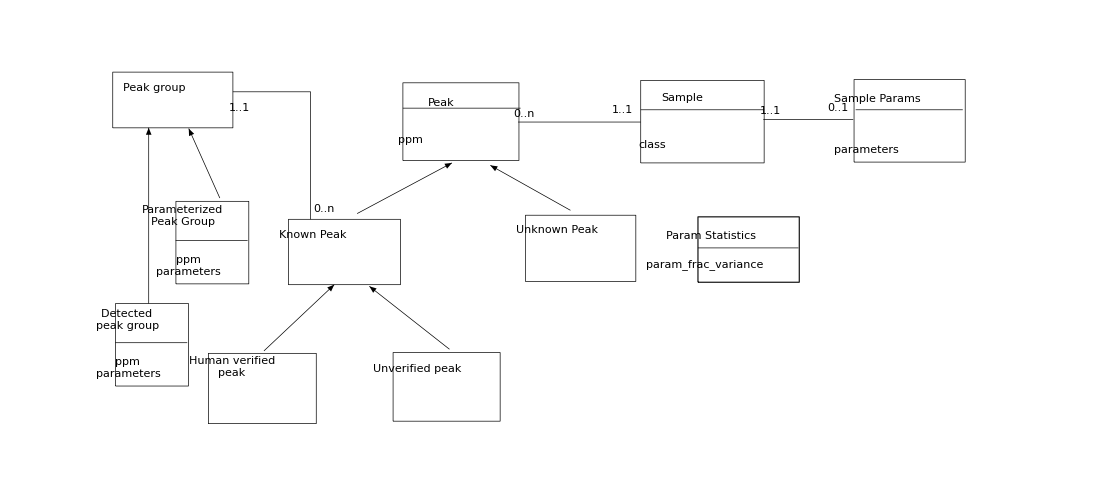

The hough tools use a file format consisting of lines of space-separated values.  The first value in each line is a type identifier.  It would be the table name in the database.  There is a table for each of the following classes: parameterized_peak_group, detected_peak_group, sample, sample_parameters, param_statistics, human_verified_peak, unverified_peak, and unknown_peak.

It is assumed that there is a peak group for any peak_group_id referenced in a known_peak object, this avoids materializing the list of peak_group_ids directly

A peak is identified by a two-part primary key: (sample_id, peak_id) - I did this because the natural way to identify peaks is to sort them by ppm within each sample and then sort the samples in some way and give the sample number and peak number.  This also makes merging new samples into the database a little easier - no need to renumber the peaks, just give each sample a unique id.

##### Fields for each table (that is each line-type)

Each table has fixed fields.  Thus each line of the file, depending on its type has well defined fields to model the relations and data shown in the table.

Each description begins with a prototype line of the file and then a description of each field.

parameterized_peak_group

parametersized_peak_group peak_group_id ppm param_1 param_2 ... param_n

peak_group_id non-negative integer uniquely identifying the peak_group to which the parameters apply

ppm the base location of the peak group

param_1 ... param_n a vector of n reaction parameters so that the predicted location of a peak in this group is ppm + peak_group.parameters · sample.sample_parameters

detected_peak_group

detected_peak_group peak_group_id ppm param_1 param_2 ... param_n

peak_group_id non-negative integer uniquely identifying the peak_group to which the parameters apply

ppm the base location of the peak group

param_1 ... param_n a vector of n reaction parameters so that the predicted location of a peak in this group is ppm + peak_group.parameters · sample.sample_parameters

human_verified_peak

human_verified_peak sample_id peak_id ppm peak_group_id

sample_id non-negative integer uniquely identifying the sample to which this peak belongs

peak_id non-negative integer uniquely identifying this peak within all peaks belonging to that sample

peak_group_id the id of the peak group to which this peak belongs

unverified_peak

unverified_peak sample_id peak_id ppm peak_group_id

Fields are the same as in human_verified_peak

unknown_peak

unknown_peak sample_id peak_id ppm

The fields are the same as in human_verified_peak

sample

sample sample_id class

sample_id a non-negative integer uniquely identifying the sample described by this line

class a string (without spaces) indicating which treatment class this sample came from.  If two samples have different strings, then they came from different classes, same string, same classes

sample_params

sample_params sample_id param_1 param_2 ... param_n

sample_id a non-negative integer uniquely identifying the samle to which these parameters apply

param_1 ... param_n a vector of n sample parameters so that the predicted location of a peak in this sample is peak_group.ppm + peak_group.parameters · sample.sample_parameters

param_stats

param_stats fracvar_1 fracvar_2 ... fracvar_n

fracvar_1 ... fracvar_n is a vector of n decimal rational numbers that give fraction of variance explained by the corresponding sample parameter in the group of known peaks used to generate the sample parameters

#### hough_sample_params

hough_sample_params options fractionVariance   <   initial_db   >   db_with_sample_params

Reads a peak database from standard input.  Extracts the set of peak_groups that have a representative in every sample.  Creates a set of sample parameters that accounts for at least fractionVariance (0..1) of the variance of the peaks in those peak groups.  Outputs a database with these new sample parameters along with a param_stats object added.

If there are already sample_params objects in the database, then three things differ.  First, the number of parameters is set to be the same as the number of parameters in the existing objects.  Second, only samples not associated with an extant sample_params object are given new sample_params objects.  Third, the param_stats object will be left unchanged.  (Maybe I should update it? - check for later version.)

##### Options

The only option is --remove-sample-params which, when present, removes all sample_params objects from the input database before processing it

#### simple_hough

simple_hough centralLocationResolution baseResolution standardDeviation max_GiB_RAM   <   initial_db   >   db_with_detected_peaks

Reads a peak database from standard input.  This database must have sample_params objects defined for every sample and also a param_stats object.  Uses the Alm et. al. Hough transform algorithm to infer the existence of peak groups.  The output database has a set of detected_peak_group objects.

centralLocationResolution gives the number of steps to use in definining the central location of the peaks.

baseResolution gives the number of steps to use for the first principal component.  If another principal component explains 25% of the variance of the first it will be given 25% of the steps.

standardDeviation gives the standard deviation of the Gaussian used in "fuzzifying" the hough transform

max_GiB_RAM gives the maximum number of GiB of RAM to use.  The program will either use partitioning methods to try and meet this constraint or exit with an error.  The program calculates only an estimate, so this is more of a suggestion than a hard rule.

#### assign_peaks

assign_peaks [keep_original_groups|keep_new_groups] singleMismatchPenalty groupMismatchPenalty  <   initial_db   >   db_with_correspondence

Reads a peak database from standard input.  This database must have detected_peak_group objects.  Does an assignment of unknown peaks to detected groups.  Many of them should become known peaks.  Then the extant known peaks are harmonized with the detected groups and newly known peaks.  Known peaks in the input that correspond to one another will continue to correspond afterwards.  However, if keep_new_groups is set, they may be given different peak parameters.  The output will have no detected_peak_group objects, and may have new parameterized_peak_group objects.  I outline the algorithm in more detail below.

Alm et. al. does not speak about peak assignment - they use the predicted locations as the peak location in each sample.  This does an assignment of peaks to detected peak groups.

First, for each sample, an assignment is made between all peaks and both the detected peak groups so as to minimize a penalty function.  For any groups that do not have a corresponding peak, a singleMismatchPenalty is charged.  Otherwise, the distance between a group's predicted location and the assigned peak location is charged.  Then any unknown peaks are changed into known peaks assigned to the group from the generated assignment.  (Note: I do not match to both groups because one expects that each peak group in a set should have a representative peak, thus it makes sense to charge a penalty.  However there is overlap between the sets - most peak groups in the original should have a corresponding group in the detected.  If I use both sets, I don't know which groups correspond so I don't know when to charge a penalty.)

Then, depending on the first parameter (whether it is keep_original_groups or keep_new_groups), the group that is to be discarded is matched in the as done with the sample peaks to the group that is to be kept.  An discarded group with no match is charged a groupMismatchPenalty.  A discarded group with a match is charged a penalty according to the total error of its peaks in the matched kept group.  Finally, any known peaks in a discarded group with a match are moved to a the kept group and the discarded group is removed.  Those "discarded" groups with no match are kept.  At the end, all remaining detected_peak_group objects are promoted to parameterized peak group objects.

## 28 April 2011 Thursday

### Rewrote the specification from yesterday and put it on the wiki

Note that I am calling it a specification rather than a design since that really describes its function a little better.  There is a good bit of design there too (I specify a serialization format, executable names etc.)

### Began writing test cases for hough prototype

#### Generate test data for simple test case

##### randomPeaksAndPermutationAndParameters definition

```mathematica
randomPeaksAndPermutationAndParameters::usage="randomPeaksAndPermutationAndParameters[numPeaks,numSamples,factorStdDev,noiseStdDev,peakResponseStdDev,peakRange]

Exactly like randomPeaksAndPermutation except has 4 more rules in the output: \"correctly_ordered_peaks\", \"peak_params\", \"peak_ppms\", and \"sample_params\"

Note that the peak_params and peak_ppms are given for the corresponding indices in the correctly ordered peaks.
";
```

```mathematica
randomPeaksAndPermutationAndParameters[numPeaks_Integer,numSamples_Integer,factorStdDev_List,noiseStdDev_,peakResponseStdDev_List,peakRange_List]/;Length[factorStdDev]==Length[peakResponseStdDev]&&NumberQ[noiseStdDev]&&noiseStdDev>0&&Length[peakRange]==2:=
With[{
s=Table[factorStdDev RandomReal[NormalDistribution[0,1],Length[factorStdDev]],{numSamples}],
a=Table[peakResponseStdDev RandomReal[NormalDistribution[0,1],Length[peakResponseStdDev]],{numPeaks}],
k=RandomReal[peakRange,numPeaks]},
With[{rawPos=Map[Function[sj,MapThread[Function[{ai,ki},ki+Dot[ai, sj]+RandomReal[NormalDistribution[0,noiseStdDev]]],{a,k}]],s]},
With[{sortOrdering=Map[Ordering,rawPos],
sortedPos=Map[Sort,rawPos]},
With[{unsortOrdering=Map[Ordering,sortOrdering]},
{"peaks"->sortedPos,"permutation"->unsortOrdering,"correctly_ordered_peaks"->rawPos,"peak_params"->a,"peak_ppms"->k,"sample_params"->s}
]]]]
```

##### Generating the test data

```mathematica
?randomPeaksAndPermutation
```

"randomPeaksAndPermutation[numPeaks,numSamples,factorStdDev,noiseStdDev,peakResponseStdDev,peakRange] \n\nReturns a list of rules {\"peaks\"→...,\"permutation\"→...}.\n\n\"peaks\" gives a list of samples, each sample is a list of peaks sorted by their location.\n\n\"permutation\" gives a list of permutations that, when applied to the corresponding sample, will make the i^th position in that sample contain the position of the i^th peak.  Thus, after applying all the permutations, the corresponding positions in the sample will contain corresponding peaks.\n\nnumPeaks and numSamples determine how many peaks and samples will be generated\n\nEach sample has a number of latent factors s_j.  Each peak has the same number of latent response variables a_i.  Each peak also has a base location k_i.  The latent factors are selected from a multidimensional Gaussian with mean 0 and standard deviations given by factorStdDev.  Similarly the responses are selected from a Gaussian with mean 0 and standard deviations in peakResponseStdDev.  The peak means are selected independently from a uniform distribution over peakRange.\n\nThe i^th peak in the j^th sample is given a location:\nδ_ij=k_i+a_i·s_j+ξ_ij\n\nWhere ξ_ij is a normally distributed random variable with mean 0 and standard deviation noiseStdDev."

```mathematica
combinedFirstTestSample =randomPeaksAndPermutationAndParameters[10,100,{1},0.0000001,{1},{0,11}]
```

```mathematica
?applyCandidate
```

Global`applyCandidate

applyCandidate[candidate_List,initialPositions_List]:=MapThread[#2⟦#1⟧&,{candidate,initialPositions}]

```mathematica
correctPeaks="correctly_ordered_peaks"/.combinedFirstTestSample;
```

```mathematica
incorrectPeaks="peaks"/.combinedFirstTestSample;
```

```mathematica
perm="permutation"/.combinedFirstTestSample;
```

Verify that applyCandidate provides the way to interpret "permutation" above

```mathematica
applyCandidate[perm[[1;;2]],incorrectPeaks[[1;;2]]]
```

{{5.9022,10.7741,0.75539,9.00214,9.48405,7.12661,10.2916,0.706239,10.6325,10.393},{7.20063,9.56785,0.296305,11.1315,6.46664,10.8757,9.87441,2.07801,13.0677,12.2951}}

```mathematica
correctPeaks[[1;;2]]
```

{{5.9022,10.7741,0.75539,9.00214,9.48405,7.12661,10.2916,0.706239,10.6325,10.393},{7.20063,9.56785,0.296305,11.1315,6.46664,10.8757,9.87441,2.07801,13.0677,12.2951}}

##### Gave up generating the data in Mathematica - I think Ruby will be conceptually easier

### Hough algorithm robustness evaluation

Some quick ideas on ways to evaluate the robustness of the hough algorithm

#### Data sources

1. Synthetic data from the model -- can see what the effects of different amounts of noise are.  Easy to generate.

2. Hand-labeled real data -- how can I be sure I've labeled it right?  Not so many samples.

3. Tuned synthetic data - using known compounds (from a DB) and their reactions to certain physical parameters, generate random parameters and then put the artificially generated peaks in the right place

4. Arabadopsis dataset in the initial paper?  I need to look at this again and how THEY used it.

5. Make our own labeled data using similar techniques as those used in Arabadopsis (proly very expensive, but I had to mention it)

#### Questions to test

Also, how does lack of data affect the algorithm -- accuracy as number of samples/number of peaks/number of initially known peaks decreases?

How do errors in the known peaks affect the algorithm?

How does the algorithm do using "known" peaks from another algorithm?

How does noise in the various parameters affect the algorithm.

What about systematic errors caused by, for example, incorrect baseline shift or distortions near the water signal.

## 29 April - 1 May 2011 Friday-Sunday

### Wrote test cases for hough transform prototype

## 2 May 2011 Monday

### Wrote test cases and code for hough transform prototype

### Set up documentation for hough transform prototoype

### Idea: eliminate peak position axis by solving for maxima analytically

One axis of the hough transform will need to be the parameters of each peak.  Alm et. al. fill the accumulators with votes that are equal-width gaussians centered on the predicted parameter values to get a given peak.  To save space at the expense of time, we could generate the accumulators only when we need them after all peaks have been examined.

However, this idea goes farther - don't search an array of accumulators for the maxima.  Just solve for them analytically.  Gaussians are (mostly) well-behaved functions and we are just summing them.  However, as you see below, solving the equation analytically isn't that simple.

```mathematica
gaussian[x_,μ_,σ_]:=Exp[-((x-μ)/σ)^2]
```

Looking at the case of only two peaks.  Without loss of generality, we can shift the axis so that the first peak has 0 mean and scale the axis so σ=1.  Let n be the mean of the second peak.

```mathematica
twopeaks=gaussian[x,0,1]+gaussian[x,n,1]
```

ⅇ^(-x^2)+ⅇ^(-(-n+x)^2)

Take first derivative

```mathematica
twopeaksderiv=D[twopeaks,x]
```

-2 ⅇ^(-x^2) x-2 ⅇ^(-(-n+x)^2) (-n+x)

Solve for zeroes - but Mathematica can't do it analytically

```mathematica
Reduce[twopeaksderiv==0,{x},Reals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[-2 ⅇ^(-x^2) x-2 ⅇ^(-(-n+x)^2) (-n+x)==0,{x},Reals]

So, try with some test values to get an idea (after trying a bunch, it seems that the collapse from 3 optima to 1 optimum takes place when movable mean is located in the interval [-√2,√2], in other words, when n^2≤2

```mathematica
Sqrt[2]//N
```

1.41421

```mathematica
With[{nval=-Sqrt[2]-Power[10,-30]},{nval/2//N,Reduce[(twopeaksderiv/.{n->nval})==0,{x},Reals]//N}]
```

{-0.707107,x==-0.707107||x==-0.707107||x==-0.707107}

```mathematica
Reduce[twopeaksderiv==0&&n^2<2,Reals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[-2 ⅇ^(-x^2) x-2 ⅇ^(-(-n+x)^2) (-n+x)==0&&n^2<2,Reals]

```mathematica
Simplify[(x-n)^2-(x-m)^2]
```

-(m-n) (m+n-2 x)

```mathematica
Manipulate[Plot[Exp[-x^2]+Exp[-(x-n/10)^2],{x,-10,10},PlotRange->All],{n,-20,20}]
```

```mathematica
Manipulate[Plot[{x,n/(Exp[-2x n]Exp[n^2]+1)},{x,-10,10},PlotRange->{-n,n}],{n,-3,3}]
```

### Looked at numerical stability of polar box-muller

```mathematica
Needs["PlotLegends`"]
```

The plot below shows that the multiplicand in the polar version decreases MUCH faster as you get close to 0, giving potentially much larger values.  The polar form is also always less than the normal form.  The only place there will be a stability problem is near 0 where the slope is large (and thus small input errors give rise to large output errors) near 1, there should not be a problem

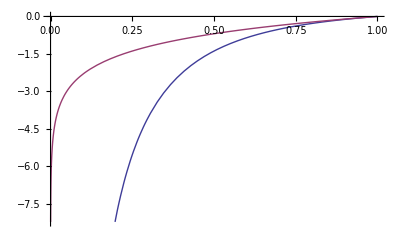

```mathematica
Plot[{Log[s]/s,Log[s]},{s,0,1},PlotLegend->{Log[s]/s,Log[s]},LegendPosition->{0,-0.4}]
```

```mathematica
Reduce[Log[x]<-k&&k>1&&x>0&&x<1,{x},Reals]
```

k>1&&0<x<ⅇ^-k

```mathematica
Reduce[(Log[x]/x)<-k&&k>1&&x>0&&x<1,{x},Reals]
```

k>1&&0<x<ⅇ^(-ProductLog[k])

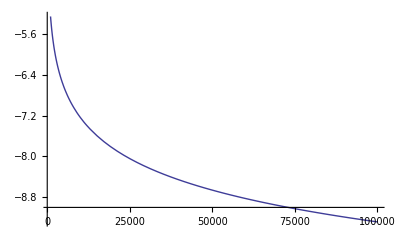

```mathematica
Plot[-ProductLog[k],{k,1000,100000}]
```

```mathematica
Reduce[Log[s]/s<Log[s]&&s>0&&s<1,Reals]
```

0<s<1

## 3 May 2011 Tuesday

### Set up documentation for hough transform prototype